### Log of changes

14.5.18 Note:  I changed throwP and intSNP to include t^* as well as r^*, for consistency.

10/2/18 Note: Included the updated pedigree files and the flipped allele labelling - which should now be consistent between the three lines.

4/2/18 Note:  I moved the analysis of the individual data from November to a new notebook “Analysing individual data”

28/7/17 Note:  These definitions were extracted from the bloated “Selection on pedigrees” notebook, and should be used as the reference for processing the Longshanks data

## Data

### Summary of files (to do)

There are three sets of data files - and annoyingly, each has a subset of what is needed. The last set, which I had optimistically labelled “all” has sex of all individuals, but not body mass data; also, an individual is missing in generation 15. Actually, sex is coded within the individual labels, and so can be extracted from the second dataset.

The  SNP positions take up more space than the counts, because they are long integers.

### Pedigree: LS1_pedigree.pruned.ped.csv …

The old files LS#_pedigree.pruned.ped.csv are now replaced with LS1_pedigree.pruned.ped.F17_ 32 _mod and LS2_pedigree.pruned.labels.ped.F17_29_mod. The latter have added a few mice in generation 17 that were genotyped, but not parents. It is important that genotypes match the pedigree, so that simulations conditioned on the pedigree are consistent with the sampled allele frequencies.

Note: I changed the file names slightly to make them consistent with each other.

However, there remains the unavoidable problem that some of the founders were not genotyped, which substantially complicates the analysis.

#### Reading in pedigree

```mathematica
{FileNameSetter[Dynamic[pedLS1]],FileNameSetter[Dynamic[pedLS2]]}
```

{$CellContext`pedLS1OpenAll,$CellContext`pedLS2OpenAll}

#### pedLS

July 2017 - I deleted a file name by mistake, causing considerable trouble..

```mathematica
pedLS::usage="pedLS[j] is the file where the pedigree for LS1, LS2 are stored";
```

```mathematica
pedLS[1]= "/Manuscripts/Selection on pedigrees/LS1_pedigree.pruned.ped.F17_32_mod.csv";
pedLS[2]="/Manuscripts/Selection on pedigrees/LS2_pedigree.pruned.ped.F17_29_mod.csv";
```

#### pedLSold

```mathematica
pedLSold::usage="pedLSold[j] is the file where the pedigree for LS1, LS2 are stored; this old version does not include all the F17 genotyped mice.";
```

```mathematica
pedLSold[1]= "/Manuscripts/Selection on pedigrees/LS1_pedigree.pruned.ped.csv";
pedLSold[2]="/Manuscripts/Selection on pedigrees/LS2_pedigree.pruned.ped.csv";
```

#### dataPedLS

```mathematica
dataPedLS::usage="dataPedLS[1] is the raw data for LS1; similarly for LS2.  The first row is a header, the remainder contain {id,gen,sex,sire,dam}";
```

```mathematica
dataPedLS[r_]:=dataPedLS[r]=Import[pedLS[r],"Data"];
```

#### dataPedLSold

```mathematica
dataPedLSold::usage="dataPedLSold[1] is the raw old data for LS1; similarly for LS2.  The first row is a header, the remainder contain {id,gen,sex,sire,dam}";
```

```mathematica
dataPedLSold[r_]:=dataPedLSold[r]=Import[pedLSold[r],"Data"];
```

#### getDataPedLSold

```mathematica
getDataPedLSold::usage="getDataPedLSold[t,r] stores data for generation t∈{0…20} and replicate LSr";
```

```mathematica
getDataPedLSold[t_Integer,r:(1|2)]:=getDataPedLSold[t,r]=Cases[dataPedLSold[r],{_,("F"<>ToString[t])|("F0"<>ToString[t]),__}];
```

#### getDataPedLS

11/2/18: Mouse # 27 in generation 17 has missing parents. As a temporary bodge, I give it the same parents as mouse #28

```mathematica
getDataPedLS::usage="getDataPedLS[t,r] stores data for generation t∈{0…20} and replicate LSr";
```

```mathematica
getDataPedLS[t_Integer,r:(1|2)]:=getDataPedLS[t,r]=Module[{tt},
tt=Cases[dataPedLS[r],{_,("F"<>ToString[t])|("F0"<>ToString[t]),__}];
If[t==17∧r==1,ReplacePart[tt,27->Join[tt⟦27,{1,2,3}⟧,tt⟦28,{4,5}⟧]],tt]];
```

#### sex, inds

```mathematica
sex::usage="sex[t,r] stores sex for generation t∈{0…20} and replicate LSr; M~0, F~1";
```

```mathematica
inds::usage="inds[t,r] stores id for breeding individuals in generation t∈{0…20} and replicate LSr.  There are no such data for the control line. ";
```

```mathematica
inds[t_,r_]:=inds[t,r]=getDataPedLS[t,r]⟦All,1⟧;
sex[t_,r_]:=sex[t,r]=Switch[StringTake[#,1],"F"|"f",1,"M",0,_,∅]&/@getDataPedLS[t,r]⟦All,3⟧;
```

#### sires, dams

```mathematica
dams::usage="dams[t,r] stores the dams of each individual in genration t∈{1…20}.";sires::usage="sires[t,r] stores the sires of each individual in genration t∈{1…20}.";
```

```mathematica
sires[t_Integer,r_]:=sires[t,r]=Flatten[(Position[inds[t-1,r],#]&/@getDataPedLS[t,r]⟦All,4⟧)/.{}->0];
dams[t_Integer,r_]:=dams[t,r]=Flatten[(Position[inds[t-1,r],#]&/@getDataPedLS[t,r]⟦All,5⟧)/.{}->0]
```

#### Checks: sires and dams are the same in B, T data

The sires and dams are the same in the T, B datasets.

```mathematica
{And@@Flatten[Table[SameQ[siresT[t,r],siresB[t,r]],{t,1,20},{r,1,2}]],And@@Flatten[Table[SameQ[damsT[t,r],damsB[t,r]],{t,1,20},{r,1,2}]]}
```

{True,True}

#### pedigree (filling in missing data for LS2)

```mathematica
pedigree::usage="pedigree[r] stores a list of pedigree matrices for LSr, {P_(1 ← 0),…,P_(20 ← 19)}. In generation 5, LS2, 3 fathers and 3 mothers are filled in randomly";
```

```mathematica
pedigree[r:(1|2)]:=pedigree[r]=Module[{t,pp},
pp=Table[SparseArray[ReplacePart[ConstantArray[0,Length[inds[t-1,r]]],If[#=={0,0},{},(List/@#)->1]]&/@(Transpose[{sires[t,r],dams[t,r]}]/.{0,_}|{_,0}->{0,0})],{t,1,20}];
If[r==2,ReplacePart[pp,{{3,22,4}->1,{3,22,7}->1,{12,2,2}->1,{12,2,14}->1,{13,23,20}->1,{13,23,24}->1,{13,24,20}->1,{13,24,24}->1}],pp]];
```

Both parents are missing in generations 3, 12, 13, for #{3,22}, {12,2}, {13,23}, {13, 24}

```mathematica
Position[Normal[pedigree[2]],{0...}]
```

{{3,22},{12,2},{13,23},{13,24}}

Reassign parents:
kids | parents
{3,22} | {4,7}
{12,2} | {2,14}
{13,23} | {20,24}
{13,24} | {20,24}

```mathematica
pedigree[2]⟦3⟧//MatrixForm
```

(0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
pedigree[2]⟦12⟧//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
pedigree[2]⟦13⟧//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

#### Checking the missing pedigree data

It seems that the data on parents for generation 5 is missing in both datasets:

```mathematica
Transpose[{sires[5,2],dams[5,2]}]
```

{{2,14},{5,16},{5,16},{7,0},{7,0},{9,18},{11,0},{11,0},{13,21},{15,23},{17,0},{17,0},{17,0},{0,1},{0,1},{20,4},{20,4},{20,4},{0,6},{0,6},{22,8},{22,8},{24,10},{24,10},{0,12},{0,12},{19,3},{19,3}}

```mathematica
Transpose[{Flatten[Position[inds[4,2],#]&/@indsT[4,2]⟦siresT[5,2]⟦posT[5,2]⟧⟧],Flatten[Position[inds[4,2],#]&/@indsT[4,2]⟦damsT[5,2]⟦posT[5,2]⟧⟧]}]
```

{{2,14},{5,16},{5,16},{7,0},{7,0},{9,18},{11,0},{11,0},{13,21},{15,23},{17,0},{17,0},{17,0},{0,1},{0,1},{20,4},{20,4},{20,4},{0,6},{0,6},{22,8},{22,8},{24,10},{24,10},{0,12},{0,12},{19,3},{19,3}}

### Pedigree with phenotypes: LS1_pedigree.pruned.ped.csv …

Note that control data only exist for some generations - just those that were measured.

#### Missing sires & dams in LS2 - filling in

In LS2, there are a substantial number of missing sires & dams in the pedigree.  In such cases, we need to inflate the # measured to give the correct values - even if we do not know the number to apportion to each family.

```mathematica
tt=Flatten/@Table[{Length[siresT[t,r]]+Length[damsT[t,r]],Count[siresT[t,r],0],Count[damsT[t,r],0]},{t,20},{r,2}];
Append[Prepend[tt,{"LS1: n","#∅ sires","#∅ dams","LS2: n","#∅ sires","#∅ dams"}],Total[Drop[tt,1]]]//TableForm
```

LS1: n | #∅ sires | #∅ dams | LS2: n | #∅ sires | #∅ dams
382 | 191 | 191 | 298 | 149 | 149
412 | 0 | 0 | 388 | 0 | 0
400 | 0 | 0 | 422 | 23 | 23
382 | 0 | 0 | 292 | 0 | 0
390 | 0 | 0 | 366 | 42 | 32
294 | 0 | 0 | 350 | 0 | 0
340 | 0 | 0 | 282 | 0 | 0
334 | 0 | 0 | 336 | 0 | 0
304 | 0 | 0 | 268 | 0 | 0
308 | 0 | 0 | 296 | 0 | 0
288 | 0 | 0 | 316 | 0 | 0
254 | 0 | 0 | 316 | 1 | 1
298 | 0 | 0 | 332 | 12 | 12
276 | 0 | 0 | 260 | 4 | 4
262 | 0 | 0 | 270 | 0 | 0
222 | 0 | 0 | 302 | 0 | 0
244 | 0 | 0 | 288 | 0 | 0
236 | 0 | 0 | 266 | 0 | 0
234 | 0 | 0 | 308 | 0 | 0
248 | 0 | 0 | 246 | 0 | 0
5726 | 0 | 0 | 5904 | 82 | 72

Missing values need to be assigned, to maintain the correct strength of selection (assuming that these measurements were in fact used in the rankings). A reasonable strategy is to assign the ‘spare’ individuals to those families that have no children recorded.  Family size is then {7,5} on average, in this example. Specifically:
	- find whether there are individuals with unknown parents (i.e. missing value 0 in sires or dams)
	- identify whether there are families with fewer measured individuals than required (only generation 5)
	- if so, assign the spare individuals to those families
	- if all families have sufficient individuals to allow selection, then assign the spare individuals

```mathematica
ff[kk_]:=Module[{pars,kds,nKs,kbf,nktot,sx},
sx=sex[kk,2];
pars=distinctParents[pedigree[2]⟦kk⟧];
kds=Flatten/@(Position[Parents[pedigree[2]⟦kk⟧],#]&/@pars);
nKs={Count[sx⟦#⟧,0],Count[sx⟦#⟧,1]}&/@kds;
kbf=Intersection@@kids[kk-1,2]⟦#⟧&/@pars;
nktot={Count[sexT[kk,2]⟦#⟧,0],Count[sexT[kk,2]⟦#⟧,1]}&/@kbf;
Transpose[{nktot,nKs}]];
```

Only generations {3,5,12,13,14} have offspring with missing sires and dams:

```mathematica
TableForm[tt⟦{3,5,12,13,14},{5,6}⟧]
```

23 | 23
42 | 32
1 | 1
12 | 12
4 | 4

These are the # available and selected in each case.  Only in generation 5 are there families that had too few to select; in other cases scattering the spare individuals across families should work.

```mathematica
TableForm[ff[#],TableDepth->2]&/@{3,5,12,13,14}
```

{{5,6} | {0,1}
{9,6} | {1,1}
{7,5} | {1,1}
{7,4} | {1,0}
{3,8} | {1,1}
{8,3} | {1,1}
{9,7} | {1,1}
{7,7} | {1,1}
{6,6} | {0,1}
{8,6} | {1,1}
{4,8} | {1,1}
{10,4} | {0,1}
{5,12} | {1,0},{0,0} | {1,1}
{7,5} | {1,0}
{8,10} | {1,1}
{10,6} | {2,1}
{6,5} | {1,1}
{0,0} | {1,1}
{0,0} | {1,1}
{4,9} | {1,1}
{3,1} | {1,0}
{8,4} | {1,1}
{0,0} | {1,1}
{0,0} | {1,1}
{10,8} | {0,1}
{4,1} | {0,1}
{0,0} | {1,2},{3,4} | {1,1}
{5,7} | {1,0}
{7,5} | {1,1}
{8,3} | {1,1}
{3,6} | {1,1}
{8,6} | {0,1}
{5,8} | {1,1}
{5,4} | {1,1}
{5,2} | {1,2}
{6,8} | {0,1}
{4,5} | {1,2}
{8,4} | {1,0}
{3,8} | {1,0},{6,4} | {1,0}
{3,5} | {1,1}
{3,7} | {1,2}
{8,6} | {1,1}
{8,6} | {0,1}
{9,6} | {0,1}
{4,7} | {1,2}
{5,7} | {1,1}
{6,6} | {2,1}
{4,7} | {2,1}
{8,4} | {1,1}
{5,9} | {1,0},{7,4} | {1,1}
{10,1} | {1,1}
{5,4} | {1,1}
{7,7} | {2,0}
{5,8} | {1,0}
{4,5} | {2,2}
{5,5} | {1,2}
{3,1} | {1,0}
{9,4} | {0,1}
{1,3} | {0,1}
{8,3} | {1,1}
{6,3} | {0,1}
{6,2} | {1,1}}

#### Reading in pedigree

```mathematica
{FileNameSetter[Dynamic[pedLS1tl]],FileNameSetter[Dynamic[pedLS2tl]],FileNameSetter[Dynamic[pedCtl]]}
```

{$CellContext`pedLS1tlOpenAll,$CellContext`pedLS2tlOpenAll,$CellContext`pedCtlOpenAll}

```mathematica
{FileNameSetter[Dynamic[pedLS1bm]],FileNameSetter[Dynamic[pedLS2bm]],FileNameSetter[Dynamic[pedCbm]]}
```

{$CellContext`pedLS1bmOpenAll,$CellContext`pedLS2bmOpenAll,$CellContext`pedCbmOpenAll}

#### pedLStl, pedLSbm

```mathematica
pedLSbm::usage="pedLSbm[j] is the file where the pedigree for LS1, LS2 are stored, with tbody mass; j=0 is control";
```

```mathematica
pedLSbm[0]="/Manuscripts/Selection on pedigrees/Selection_Analysis/pedigree/pedigree_C.bm.draw.txt";
pedLSbm[1]="/Manuscripts/Selection on pedigrees/Selection_Analysis/pedigree/pedigree_L1.bm.draw.txt";
pedLSbm[2]="/Manuscripts/Selection on pedigrees/Selection_Analysis/pedigree/pedigree_L2.bm.draw.txt";
```

```mathematica
pedLStl::usage="pedLStl[j] is the file where the pedigree for LS1, LS2 are stored, with tibia length; j=0 is control";
```

```mathematica
pedLStl[0]="/Manuscripts/Selection on pedigrees/Selection_Analysis/pedigree/pedigree_C.draw.tl.txt";
pedLStl[1]="/Manuscripts/Selection on pedigrees/Selection_Analysis/pedigree/pedigree_L1.draw.tl.txt";
pedLStl[2]="/Manuscripts/Selection on pedigrees/Selection_Analysis/pedigree/pedigree_L2.draw.tl.txt";
```

#### dataPedLStl, dataPedLSbm

```mathematica
dataPedLSbm::usage="dataPedLSbm[1] is the raw data for LS1; similarly for LS2 and control (0).  Contains {gen,t,ID,sireID,damID,B,sireB,damB}";
```

```mathematica
dataPedLSbm[r_]:=dataPedLSbm[r]=Import[pedLSbm[r],"Data"];
```

```mathematica
dataPedLStl::usage="dataPedLStl[1] is the raw data for LS1; similarly for LS2 and control (0).  Contains {gen,t,ID,sireID,damID,T,sireT,damT}";
```

```mathematica
dataPedLStl[r_]:=dataPedLStl[r]=Import[pedLStl[r],"Data"];
```

#### getDataPedLSbm, getDataPedLStl

```mathematica
getDataPedLStl::usage="getDataPedLStl[t,r] stores tibia length data for generation t∈{0…20} and replicate r=0, 1, 2";
```

```mathematica
getDataPedLStl[t_Integer,r:(0|1|2)]:=getDataPedLStl[t,r]=Cases[dataPedLStl[r],{_,t,__}];
```

```mathematica
getDataPedLSbm::usage="getDataPedLSbm[t,r] stores body mass data for generation t∈{0…20} and replicate r=0, 1, 2";
```

```mathematica
getDataPedLSbm[t_Integer,r:(0|1|2)]:=getDataPedLSbm[t,r]=Cases[dataPedLSbm[r],{_,t,__}];
```

#### indsT, indsB

```mathematica
indsT::usage="indsT[t,r] stores id for all individuals in generation t∈{0…20} and replicate LSr, in the order of the files that contain tibia length; the same as indsB";
```

```mathematica
indsT[t_,r_]:=indsT[t,r]=getDataPedLStl[t,r]⟦All,3⟧;
```

```mathematica
indsB::usage="indsB[t,r] stores id for all individuals in generation t∈{0…20} and replicate LSr, in the order of the files that contain body mass; the same as indsT";
```

```mathematica
indsB[t_,r_]:=indsB[t,r]=getDataPedLSbm[t,r]⟦All,3⟧;
```

The orders of individuals are the same in the T, B datasets

```mathematica
And@@Flatten[Table[SameQ[indsT[t,r],indsB[t,r]],{t,0,20},{r,0,2}]]
```

True

```mathematica
getDataPedLS[2,1]//TableForm
```

F02-A2-F-08 | F02 | F | F01-A2-M-06 | F01-B2-F-01
F02-A2-M-10 | F02 | M | F01-A2-M-06 | F01-B2-F-01
F02-B2-F-05 | F02 | F | F01-B2-M-12 | F01-C2-F-05
F02-B2-M-13 | F02 | M | F01-B2-M-12 | F01-C2-F-05
F02-C2-F-08 | F02 | F | F01-C2-M-13 | F01-D2-F-06
F02-C2-M-10 | F02 | M | F01-C2-M-13 | F01-D2-F-06
F02-D2-F-07 | F02 | F | F01-D2-M-08 | F01-E2-F-02
F02-D2-M-16 | F02 | M | F01-D2-M-08 | F01-E2-F-02
F02-E2-F-04 | F02 | F | F01-E2-M-13 | F01-F2-F-05
F02-E2-M-13 | F02 | M | F01-E2-M-13 | F01-F2-F-05
F02-F2-F-03 | F02 | F | F01-F2-M-12 | F01-G2-F-02
F02-F2-M-11 | F02 | M | F01-F2-M-12 | F01-G2-F-02
F02-G2-F-02 | F02 | F | F01-G2-M-08 | F01-H2-F-01
F02-G2-M-14 | F02 | M | F01-G2-M-08 | F01-H2-F-01
F02-H2-F-04 | F02 | F | F01-H2-M-10 | F01-I2-F-04
F02-H2-M-15 | F02 | M | F01-H2-M-10 | F01-I2-F-04
F02-I2-F-04 | F02 | F | F01-I2-M-09 | F01-J2-F-04
F02-I2-M-15 | F02 | M | F01-I2-M-09 | F01-J2-F-04
F02-K2-F-03 | F02 | F | F01-K2-M-11 | F01-L2-F-01
F02-K2-M-08 | F02 | M | F01-K2-M-11 | F01-L2-F-01
F02-L2-F-03 | F02 | F | F01-L2-M-04 | F01-M2-F-05
F02-L2-M-09 | F02 | M | F01-L2-M-04 | F01-M2-F-05
F02-M2-F-06 | F02 | F | F01-M2-M-12 | F01-N2-F-02
F02-O2-F-03 | F02 | F | F01-J2-M-06 | F01-K2-F-05
F02-O2-M-13 | F02 | M | F01-J2-M-06 | F01-K2-F-05
F02-P2-M-09 | F02 | M | F01-K2-M-10 | F01-D2-F-01

```mathematica
getDataPedLStl[2,1]//TableForm
```

F02 | 2 | F02-A1-F-01 | F01-A1-M-06 | F01-B1-F-03 | 17.183 | 18.3341 | 18.1735
F02 | 2 | F02-A1-F-02 | F01-A1-M-06 | F01-B1-F-03 | 17.8715 | 18.3341 | 18.1735
F02 | 2 | F02-A1-F-03 | F01-A1-M-06 | F01-B1-F-03 | 18.0017 | 18.3341 | 18.1735
F02 | 2 | F02-A1-F-04 | F01-A1-M-06 | F01-B1-F-03 | 18.2127 | 18.3341 | 18.1735
F02 | 2 | F02-A1-M-05 | F01-A1-M-06 | F01-B1-F-03 | 18.5772 | 18.3341 | 18.1735
F02 | 2 | F02-A1-M-06 | F01-A1-M-06 | F01-B1-F-03 | 18.2407 | 18.3341 | 18.1735
F02 | 2 | F02-A1-M-07 | F01-A1-M-06 | F01-B1-F-03 | 18.9284 | 18.3341 | 18.1735
F02 | 2 | F02-A1-M-08 | F01-A1-M-06 | F01-B1-F-03 | 19.1638 | 18.3341 | 18.1735
F02 | 2 | F02-A1-M-09 | F01-A1-M-06 | F01-B1-F-03 | 18.4777 | 18.3341 | 18.1735
F02 | 2 | F02-A1-M-10 | F01-A1-M-06 | F01-B1-F-03 | 18.0102 | 18.3341 | 18.1735
F02 | 2 | F02-A1-M-11 | F01-A1-M-06 | F01-B1-F-03 | 18.9387 | 18.3341 | 18.1735
F02 | 2 | F02-A1-M-12 | F01-A1-M-06 | F01-B1-F-03 | 18.2348 | 18.3341 | 18.1735
F02 | 2 | F02-B1-F-01 | F01-B1-M-08 | F01-C1-F-10 | 18.1989 | 18.1858 | 18.585
F02 | 2 | F02-B1-F-02 | F01-B1-M-08 | F01-C1-F-10 | 17.9747 | 18.1858 | 18.585
F02 | 2 | F02-B1-F-03 | F01-B1-M-08 | F01-C1-F-10 | 17.3225 | 18.1858 | 18.585
F02 | 2 | F02-B1-F-04 | F01-B1-M-08 | F01-C1-F-10 | 18.057 | 18.1858 | 18.585
F02 | 2 | F02-B1-F-05 | F01-B1-M-08 | F01-C1-F-10 | 17.4459 | 18.1858 | 18.585
F02 | 2 | F02-B1-F-06 | F01-B1-M-08 | F01-C1-F-10 | 18.291 | 18.1858 | 18.585
F02 | 2 | F02-B1-F-07 | F01-B1-M-08 | F01-C1-F-10 | 18.3115 | 18.1858 | 18.585
F02 | 2 | F02-B1-F-08 | F01-B1-M-08 | F01-C1-F-10 | 17.3399 | 18.1858 | 18.585
F02 | 2 | F02-B1-F-09 | F01-B1-M-08 | F01-C1-F-10 | 18.1299 | 18.1858 | 18.585
F02 | 2 | F02-B1-M-10 | F01-B1-M-08 | F01-C1-F-10 | 17.5501 | 18.1858 | 18.585
F02 | 2 | F02-B1-M-11 | F01-B1-M-08 | F01-C1-F-10 | 18.1401 | 18.1858 | 18.585
F02 | 2 | F02-B1-M-12 | F01-B1-M-08 | F01-C1-F-10 | 17.5097 | 18.1858 | 18.585
F02 | 2 | F02-B1-M-13 | F01-B1-M-08 | F01-C1-F-10 | 17.9853 | 18.1858 | 18.585
F02 | 2 | F02-B1-M-14 | F01-B1-M-08 | F01-C1-F-10 | 17.9793 | 18.1858 | 18.585
F02 | 2 | F02-B1-M-15 | F01-B1-M-08 | F01-C1-F-10 | 18.3426 | 18.1858 | 18.585
F02 | 2 | F02-B1-M-16 | F01-B1-M-08 | F01-C1-F-10 | 18.3222 | 18.1858 | 18.585
F02 | 2 | F02-C1-F-01 | F01-C1-M-05 | F01-D1-F-08 | 17.8341 | 18.512 | 18.5901
F02 | 2 | F02-C1-F-02 | F01-C1-M-05 | F01-D1-F-08 | 18.2104 | 18.512 | 18.5901
F02 | 2 | F02-C1-F-03 | F01-C1-M-05 | F01-D1-F-08 | 17.7234 | 18.512 | 18.5901
F02 | 2 | F02-C1-F-04 | F01-C1-M-05 | F01-D1-F-08 | 17.4837 | 18.512 | 18.5901
F02 | 2 | F02-C1-F-05 | F01-C1-M-05 | F01-D1-F-08 | 18.0193 | 18.512 | 18.5901
F02 | 2 | F02-C1-F-06 | F01-C1-M-05 | F01-D1-F-08 | 16.6719 | 18.512 | 18.5901
F02 | 2 | F02-C1-M-07 | F01-C1-M-05 | F01-D1-F-08 | 17.2629 | 18.512 | 18.5901
F02 | 2 | F02-C1-M-08 | F01-C1-M-05 | F01-D1-F-08 | 17.794 | 18.512 | 18.5901
F02 | 2 | F02-C1-M-09 | F01-C1-M-05 | F01-D1-F-08 | 18.2622 | 18.512 | 18.5901
F02 | 2 | F02-C1-M-10 | F01-C1-M-05 | F01-D1-F-08 | 18.176 | 18.512 | 18.5901
F02 | 2 | F02-C1-M-11 | F01-C1-M-05 | F01-D1-F-08 | 18.4167 | 18.512 | 18.5901
F02 | 2 | F02-C1-M-12 | F01-C1-M-05 | F01-D1-F-08 | 18.3494 | 18.512 | 18.5901
F02 | 2 | F02-C1-M-13 | F01-C1-M-05 | F01-D1-F-08 | 18.2395 | 18.512 | 18.5901
F02 | 2 | F02-C1-M-14 | F01-C1-M-05 | F01-D1-F-08 | 18.0069 | 18.512 | 18.5901
F02 | 2 | F02-C1-M-15 | F01-C1-M-05 | F01-D1-F-08 | 18.3381 | 18.512 | 18.5901
F02 | 2 | F02-D1-F-01 | F01-D1-M-11 | F01-E1-F-07 | 18.4214 | 18.8394 | 19.0795
F02 | 2 | F02-D1-F-02 | F01-D1-M-11 | F01-E1-F-07 | 18.0624 | 18.8394 | 19.0795
F02 | 2 | F02-D1-F-03 | F01-D1-M-11 | F01-E1-F-07 | 18.7203 | 18.8394 | 19.0795
F02 | 2 | F02-D1-F-04 | F01-D1-M-11 | F01-E1-F-07 | 17.8895 | 18.8394 | 19.0795
F02 | 2 | F02-D1-F-05 | F01-D1-M-11 | F01-E1-F-07 | 18.6869 | 18.8394 | 19.0795
F02 | 2 | F02-D1-F-06 | F01-D1-M-11 | F01-E1-F-07 | 18.2089 | 18.8394 | 19.0795
F02 | 2 | F02-D1-F-07 | F01-D1-M-11 | F01-E1-F-07 | 18.5077 | 18.8394 | 19.0795
F02 | 2 | F02-D1-F-08 | F01-D1-M-11 | F01-E1-F-07 | 18.4265 | 18.8394 | 19.0795
F02 | 2 | F02-D1-F-09 | F01-D1-M-11 | F01-E1-F-07 | 18.0841 | 18.8394 | 19.0795
F02 | 2 | F02-D1-M-10 | F01-D1-M-11 | F01-E1-F-07 | 18.0094 | 18.8394 | 19.0795
F02 | 2 | F02-D1-M-11 | F01-D1-M-11 | F01-E1-F-07 | 18.1669 | 18.8394 | 19.0795
F02 | 2 | F02-D1-M-12 | F01-D1-M-11 | F01-E1-F-07 | 17.7549 | 18.8394 | 19.0795
F02 | 2 | F02-D1-M-13 | F01-D1-M-11 | F01-E1-F-07 | 17.9262 | 18.8394 | 19.0795
F02 | 2 | F02-D1-M-14 | F01-D1-M-11 | F01-E1-F-07 | 18.9477 | 18.8394 | 19.0795
F02 | 2 | F02-E1-F-01 | F01-E1-M-12 | F01-F1-F-06 | 18.2774 | 19.5301 | 18.3381
F02 | 2 | F02-E1-F-02 | F01-E1-M-12 | F01-F1-F-06 | 17.3029 | 19.5301 | 18.3381
F02 | 2 | F02-E1-F-03 | F01-E1-M-12 | F01-F1-F-06 | 18.0326 | 19.5301 | 18.3381
F02 | 2 | F02-E1-F-04 | F01-E1-M-12 | F01-F1-F-06 | 18.3704 | 19.5301 | 18.3381
F02 | 2 | F02-E1-F-05 | F01-E1-M-12 | F01-F1-F-06 | 17.8528 | 19.5301 | 18.3381
F02 | 2 | F02-E1-F-06 | F01-E1-M-12 | F01-F1-F-06 | 18.0193 | 19.5301 | 18.3381
F02 | 2 | F02-E1-F-07 | F01-E1-M-12 | F01-F1-F-06 | 17.7375 | 19.5301 | 18.3381
F02 | 2 | F02-E1-F-08 | F01-E1-M-12 | F01-F1-F-06 | 17.8236 | 19.5301 | 18.3381
F02 | 2 | F02-E1-M-09 | F01-E1-M-12 | F01-F1-F-06 | 17.6661 | 19.5301 | 18.3381
F02 | 2 | F02-E1-M-10 | F01-E1-M-12 | F01-F1-F-06 | 17.4366 | 19.5301 | 18.3381
F02 | 2 | F02-E1-M-11 | F01-E1-M-12 | F01-F1-F-06 | 18.0077 | 19.5301 | 18.3381
F02 | 2 | F02-E1-M-12 | F01-E1-M-12 | F01-F1-F-06 | 17.9215 | 19.5301 | 18.3381
F02 | 2 | F02-E1-M-13 | F01-E1-M-12 | F01-F1-F-06 | 18.0841 | 19.5301 | 18.3381
F02 | 2 | F02-E1-M-14 | F01-E1-M-12 | F01-F1-F-06 | 18.0841 | 19.5301 | 18.3381
F02 | 2 | F02-F1-F-01 | F01-F1-M-08 | F01-G1-F-03 | 18.273 | 18.5639 | 18.5671
F02 | 2 | F02-F1-F-02 | F01-F1-M-08 | F01-G1-F-03 | 18.1506 | 18.5639 | 18.5671
F02 | 2 | F02-F1-F-03 | F01-F1-M-08 | F01-G1-F-03 | 17.7502 | 18.5639 | 18.5671
F02 | 2 | F02-F1-F-04 | F01-F1-M-08 | F01-G1-F-03 | 17.3383 | 18.5639 | 18.5671
F02 | 2 | F02-F1-F-05 | F01-F1-M-08 | F01-G1-F-03 | 17.4264 | 18.5639 | 18.5671
F02 | 2 | F02-F1-F-06 | F01-F1-M-08 | F01-G1-F-03 | 17.8382 | 18.5639 | 18.5671
F02 | 2 | F02-F1-F-07 | F01-F1-M-08 | F01-G1-F-03 | 17.5008 | 18.5639 | 18.5671
F02 | 2 | F02-F1-M-08 | F01-F1-M-08 | F01-G1-F-03 | 18.1684 | 18.5639 | 18.5671
F02 | 2 | F02-F1-M-09 | F01-F1-M-08 | F01-G1-F-03 | 17.937 | 18.5639 | 18.5671
F02 | 2 | F02-F1-M-10 | F01-F1-M-08 | F01-G1-F-03 | 17.0963 | 18.5639 | 18.5671
F02 | 2 | F02-F1-M-11 | F01-F1-M-08 | F01-G1-F-03 | 18.1066 | 18.5639 | 18.5671
F02 | 2 | F02-F1-M-12 | F01-F1-M-08 | F01-G1-F-03 | 18.0008 | 18.5639 | 18.5671
F02 | 2 | F02-F1-M-13 | F01-F1-M-08 | F01-G1-F-03 | 18.0493 | 18.5639 | 18.5671
F02 | 2 | F02-F1-M-14 | F01-F1-M-08 | F01-G1-F-03 | 17.6737 | 18.5639 | 18.5671
F02 | 2 | F02-F1-M-15 | F01-F1-M-08 | F01-G1-F-03 | 17.524 | 18.5639 | 18.5671
F02 | 2 | F02-F1-M-16 | F01-F1-M-08 | F01-G1-F-03 | 17.8 | 18.5639 | 18.5671
F02 | 2 | F02-G1-F-01 | F01-G1-M-09 | F01-H1-F-08 | 18.3153 | 18.9196 | 18.0758
F02 | 2 | F02-G1-F-02 | F01-G1-M-09 | F01-H1-F-08 | 18.5077 | 18.9196 | 18.0758
F02 | 2 | F02-G1-F-03 | F01-G1-M-09 | F01-H1-F-08 | 17.6891 | 18.9196 | 18.0758
F02 | 2 | F02-G1-F-04 | F01-G1-M-09 | F01-H1-F-08 | 17.6875 | 18.9196 | 18.0758
F02 | 2 | F02-G1-F-05 | F01-G1-M-09 | F01-H1-F-08 | 17.9058 | 18.9196 | 18.0758
F02 | 2 | F02-G1-F-06 | F01-G1-M-09 | F01-H1-F-08 | 17.7486 | 18.9196 | 18.0758
F02 | 2 | F02-G1-F-07 | F01-G1-M-09 | F01-H1-F-08 | 17.8281 | 18.9196 | 18.0758
F02 | 2 | F02-G1-F-08 | F01-G1-M-09 | F01-H1-F-08 | 17.8364 | 18.9196 | 18.0758
F02 | 2 | F02-G1-F-09 | F01-G1-M-09 | F01-H1-F-08 | 18.1942 | 18.9196 | 18.0758
F02 | 2 | F02-G1-M-10 | F01-G1-M-09 | F01-H1-F-08 | 17.5835 | 18.9196 | 18.0758
F02 | 2 | F02-G1-M-11 | F01-G1-M-09 | F01-H1-F-08 | 18.2041 | 18.9196 | 18.0758
F02 | 2 | F02-G1-M-12 | F01-G1-M-09 | F01-H1-F-08 | 18.0902 | 18.9196 | 18.0758
F02 | 2 | F02-G1-M-13 | F01-G1-M-09 | F01-H1-F-08 | 18.3381 | 18.9196 | 18.0758
F02 | 2 | F02-G1-M-14 | F01-G1-M-09 | F01-H1-F-08 | 18.1735 | 18.9196 | 18.0758
F02 | 2 | F02-G1-M-15 | F01-G1-M-09 | F01-H1-F-08 | 18.0839 | 18.9196 | 18.0758
F02 | 2 | F02-G1-M-16 | F01-G1-M-09 | F01-H1-F-08 | 17.794 | 18.9196 | 18.0758
F02 | 2 | F02-G1-M-17 | F01-G1-M-09 | F01-H1-F-08 | 18.1324 | 18.9196 | 18.0758
F02 | 2 | F02-G1-M-18 | F01-G1-M-09 | F01-H1-F-08 | 18.4287 | 18.9196 | 18.0758
F02 | 2 | F02-H1-F-01 | F01-H1-M-15 | F01-I1-F-03 | 17.8569 | 18.1018 | 18.1265
F02 | 2 | F02-H1-F-02 | F01-H1-M-15 | F01-I1-F-03 | 18.2508 | 18.1018 | 18.1265
F02 | 2 | F02-H1-F-03 | F01-H1-M-15 | F01-I1-F-03 | 17.9167 | 18.1018 | 18.1265
F02 | 2 | F02-H1-F-04 | F01-H1-M-15 | F01-I1-F-03 | 17.8351 | 18.1018 | 18.1265
F02 | 2 | F02-H1-F-05 | F01-H1-M-15 | F01-I1-F-03 | 18.4235 | 18.1018 | 18.1265
F02 | 2 | F02-H1-M-06 | F01-H1-M-15 | F01-I1-F-03 | 18.3364 | 18.1018 | 18.1265
F02 | 2 | F02-H1-M-07 | F01-H1-M-15 | F01-I1-F-03 | 17.505 | 18.1018 | 18.1265
F02 | 2 | F02-H1-M-08 | F01-H1-M-15 | F01-I1-F-03 | 18.5161 | 18.1018 | 18.1265
F02 | 2 | F02-H1-M-09 | F01-H1-M-15 | F01-I1-F-03 | 18.6363 | 18.1018 | 18.1265
F02 | 2 | F02-H1-M-10 | F01-H1-M-15 | F01-I1-F-03 | 18.6339 | 18.1018 | 18.1265
F02 | 2 | F02-H1-M-11 | F01-H1-M-15 | F01-I1-F-03 | 18.2774 | 18.1018 | 18.1265
F02 | 2 | F02-H1-M-12 | F01-H1-M-15 | F01-I1-F-03 | 17.9277 | 18.1018 | 18.1265
F02 | 2 | F02-H1-M-13 | F01-H1-M-15 | F01-I1-F-03 | 18.2912 | 18.1018 | 18.1265
F02 | 2 | F02-I1-F-01 | F01-I1-M-12 | F01-J1-F-02 | 17.799 | 18.7012 | 18.5745
F02 | 2 | F02-I1-F-02 | F01-I1-M-12 | F01-J1-F-02 | 18.0881 | 18.7012 | 18.5745
F02 | 2 | F02-I1-F-03 | F01-I1-M-12 | F01-J1-F-02 | 17.6675 | 18.7012 | 18.5745
F02 | 2 | F02-I1-F-04 | F01-I1-M-12 | F01-J1-F-02 | 17.4811 | 18.7012 | 18.5745
F02 | 2 | F02-I1-F-05 | F01-I1-M-12 | F01-J1-F-02 | 18.0193 | 18.7012 | 18.5745
F02 | 2 | F02-I1-F-06 | F01-I1-M-12 | F01-J1-F-02 | 18.0031 | 18.7012 | 18.5745
F02 | 2 | F02-I1-F-07 | F01-I1-M-12 | F01-J1-F-02 | 17.6792 | 18.7012 | 18.5745
F02 | 2 | F02-I1-F-08 | F01-I1-M-12 | F01-J1-F-02 | 18.3186 | 18.7012 | 18.5745
F02 | 2 | F02-I1-M-09 | F01-I1-M-12 | F01-J1-F-02 | 18.1921 | 18.7012 | 18.5745
F02 | 2 | F02-I1-M-10 | F01-I1-M-12 | F01-J1-F-02 | 17.8429 | 18.7012 | 18.5745
F02 | 2 | F02-I1-M-11 | F01-I1-M-12 | F01-J1-F-02 | 18.5068 | 18.7012 | 18.5745
F02 | 2 | F02-I1-M-12 | F01-I1-M-12 | F01-J1-F-02 | 18.0195 | 18.7012 | 18.5745
F02 | 2 | F02-I1-M-13 | F01-I1-M-12 | F01-J1-F-02 | 18.0902 | 18.7012 | 18.5745
F02 | 2 | F02-K1-F-01 | F01-K1-M-09 | F01-L1-F-05 | 18.5667 | 18.4184 | 18.548
F02 | 2 | F02-K1-F-02 | F01-K1-M-09 | F01-L1-F-05 | 17.4581 | 18.4184 | 18.548
F02 | 2 | F02-K1-F-03 | F01-K1-M-09 | F01-L1-F-05 | 17.9482 | 18.4184 | 18.548
F02 | 2 | F02-K1-F-04 | F01-K1-M-09 | F01-L1-F-05 | 17.6472 | 18.4184 | 18.548
F02 | 2 | F02-K1-F-05 | F01-K1-M-09 | F01-L1-F-05 | 17.9494 | 18.4184 | 18.548
F02 | 2 | F02-K1-F-06 | F01-K1-M-09 | F01-L1-F-05 | 18.2064 | 18.4184 | 18.548
F02 | 2 | F02-K1-F-07 | F01-K1-M-09 | F01-L1-F-05 | 18.177 | 18.4184 | 18.548
F02 | 2 | F02-K1-F-08 | F01-K1-M-09 | F01-L1-F-05 | 17.501 | 18.4184 | 18.548
F02 | 2 | F02-K1-F-09 | F01-K1-M-09 | F01-L1-F-05 | 17.9618 | 18.4184 | 18.548
F02 | 2 | F02-K1-F-10 | F01-K1-M-09 | F01-L1-F-05 | 17.7051 | 18.4184 | 18.548
F02 | 2 | F02-K1-M-11 | F01-K1-M-09 | F01-L1-F-05 | 17.5408 | 18.4184 | 18.548
F02 | 2 | F02-K1-M-12 | F01-K1-M-09 | F01-L1-F-05 | 17.5218 | 18.4184 | 18.548
F02 | 2 | F02-K1-M-13 | F01-K1-M-09 | F01-L1-F-05 | 17.988 | 18.4184 | 18.548
F02 | 2 | F02-K1-M-14 | F01-K1-M-09 | F01-L1-F-05 | 18.0195 | 18.4184 | 18.548
F02 | 2 | F02-K1-M-15 | F01-K1-M-09 | F01-L1-F-05 | 17.9546 | 18.4184 | 18.548
F02 | 2 | F02-K1-M-16 | F01-K1-M-09 | F01-L1-F-05 | 18.176 | 18.4184 | 18.548
F02 | 2 | F02-L1-F-01 | F01-L1-M-13 | F01-M1-F-07 | 17.3534 | 18.2029 | 18.3333
F02 | 2 | F02-L1-F-02 | F01-L1-M-13 | F01-M1-F-07 | 17.9184 | 18.2029 | 18.3333
F02 | 2 | F02-L1-F-03 | F01-L1-M-13 | F01-M1-F-07 | 17.6777 | 18.2029 | 18.3333
F02 | 2 | F02-L1-F-04 | F01-L1-M-13 | F01-M1-F-07 | 18.1158 | 18.2029 | 18.3333
F02 | 2 | F02-L1-F-05 | F01-L1-M-13 | F01-M1-F-07 | 18.0094 | 18.2029 | 18.3333
F02 | 2 | F02-L1-F-06 | F01-L1-M-13 | F01-M1-F-07 | 17.6737 | 18.2029 | 18.3333
F02 | 2 | F02-L1-F-07 | F01-L1-M-13 | F01-M1-F-07 | 17.8613 | 18.2029 | 18.3333
F02 | 2 | F02-L1-F-08 | F01-L1-M-13 | F01-M1-F-07 | 18.0472 | 18.2029 | 18.3333
F02 | 2 | F02-L1-F-09 | F01-L1-M-13 | F01-M1-F-07 | 17.4264 | 18.2029 | 18.3333
F02 | 2 | F02-L1-M-10 | F01-L1-M-13 | F01-M1-F-07 | 17.8715 | 18.2029 | 18.3333
F02 | 2 | F02-L1-M-11 | F01-L1-M-13 | F01-M1-F-07 | 18.0326 | 18.2029 | 18.3333
F02 | 2 | F02-L1-M-12 | F01-L1-M-13 | F01-M1-F-07 | 17.7502 | 18.2029 | 18.3333
F02 | 2 | F02-L1-M-13 | F01-L1-M-13 | F01-M1-F-07 | 18.4485 | 18.2029 | 18.3333
F02 | 2 | F02-L1-M-14 | F01-L1-M-13 | F01-M1-F-07 | 18.585 | 18.2029 | 18.3333
F02 | 2 | F02-M1-F-01 | F01-M1-M-14 | F01-N1-F-01 | 17.6046 | 18.8394 | 18.114
F02 | 2 | F02-M1-F-02 | F01-M1-M-14 | F01-N1-F-01 | 18.0048 | 18.8394 | 18.114
F02 | 2 | F02-M1-F-03 | F01-M1-M-14 | F01-N1-F-01 | 18.1265 | 18.8394 | 18.114
F02 | 2 | F02-M1-F-04 | F01-M1-M-14 | F01-N1-F-01 | 17.5865 | 18.8394 | 18.114
F02 | 2 | F02-M1-F-05 | F01-M1-M-14 | F01-N1-F-01 | 18.111 | 18.8394 | 18.114
F02 | 2 | F02-M1-F-06 | F01-M1-M-14 | F01-N1-F-01 | 17.8662 | 18.8394 | 18.114
F02 | 2 | F02-M1-M-07 | F01-M1-M-14 | F01-N1-F-01 | 17.2321 | 18.8394 | 18.114
F02 | 2 | F02-M1-M-08 | F01-M1-M-14 | F01-N1-F-01 | 17.5032 | 18.8394 | 18.114
F02 | 2 | F02-M1-M-09 | F01-M1-M-14 | F01-N1-F-01 | 17.6675 | 18.8394 | 18.114
F02 | 2 | F02-M1-M-10 | F01-M1-M-14 | F01-N1-F-01 | 18.1066 | 18.8394 | 18.114
F02 | 2 | F02-M1-M-11 | F01-M1-M-14 | F01-N1-F-01 | 18.4551 | 18.8394 | 18.114
F02 | 2 | F02-M1-M-12 | F01-M1-M-14 | F01-N1-F-01 | 17.7279 | 18.8394 | 18.114
F02 | 2 | F02-M1-M-13 | F01-M1-M-14 | F01-N1-F-01 | 17.8965 | 18.8394 | 18.114
F02 | 2 | F02-M1-M-14 | F01-M1-M-14 | F01-N1-F-01 | 18.0472 | 18.8394 | 18.114
F02 | 2 | F02-N1-F-01 | F01-N1-M-06 | F01-A1-F-12 | 17.7108 | 18.6199 | 18.0285
F02 | 2 | F02-N1-F-02 | F01-N1-M-06 | F01-A1-F-12 | 18.2654 | 18.6199 | 18.0285
F02 | 2 | F02-N1-F-03 | F01-N1-M-06 | F01-A1-F-12 | 18.0841 | 18.6199 | 18.0285
F02 | 2 | F02-N1-F-04 | F01-N1-M-06 | F01-A1-F-12 | 17.911 | 18.6199 | 18.0285
F02 | 2 | F02-N1-F-05 | F01-N1-M-06 | F01-A1-F-12 | 17.936 | 18.6199 | 18.0285
F02 | 2 | F02-N1-F-06 | F01-N1-M-06 | F01-A1-F-12 | 18.4319 | 18.6199 | 18.0285
F02 | 2 | F02-N1-F-07 | F01-N1-M-06 | F01-A1-F-12 | 18.3398 | 18.6199 | 18.0285
F02 | 2 | F02-N1-F-08 | F01-N1-M-06 | F01-A1-F-12 | 18.1108 | 18.6199 | 18.0285
F02 | 2 | F02-N1-F-09 | F01-N1-M-06 | F01-A1-F-12 | 18.0835 | 18.6199 | 18.0285
F02 | 2 | F02-N1-F-10 | F01-N1-M-06 | F01-A1-F-12 | 18.388 | 18.6199 | 18.0285
F02 | 2 | F02-N1-M-11 | F01-N1-M-06 | F01-A1-F-12 | 18.0378 | 18.6199 | 18.0285
F02 | 2 | F02-N1-M-12 | F01-N1-M-06 | F01-A1-F-12 | 18.0518 | 18.6199 | 18.0285
F02 | 2 | F02-N1-M-13 | F01-N1-M-06 | F01-A1-F-12 | 17.7032 | 18.6199 | 18.0285
F02 | 2 | F02-N1-M-14 | F01-N1-M-06 | F01-A1-F-12 | 18.3818 | 18.6199 | 18.0285
F02 | 2 | F02-N1-M-15 | F01-N1-M-06 | F01-A1-F-12 | 18.3443 | 18.6199 | 18.0285
F02 | 2 | F02-O1-F-01 | F01-E1-M-11 | F01-D1-F-04 | 18.2332 | 19.4131 | 19.1378
F02 | 2 | F02-O1-F-02 | F01-E1-M-11 | F01-D1-F-04 | 18.7159 | 19.4131 | 19.1378
F02 | 2 | F02-O1-F-03 | F01-E1-M-11 | F01-D1-F-04 | 18.3532 | 19.4131 | 19.1378
F02 | 2 | F02-O1-F-04 | F01-E1-M-11 | F01-D1-F-04 | 18.7552 | 19.4131 | 19.1378
F02 | 2 | F02-O1-F-05 | F01-E1-M-11 | F01-D1-F-04 | 18.4485 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-06 | F01-E1-M-11 | F01-D1-F-04 | 18.6832 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-07 | F01-E1-M-11 | F01-D1-F-04 | 18.6192 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-08 | F01-E1-M-11 | F01-D1-F-04 | 18.2029 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-09 | F01-E1-M-11 | F01-D1-F-04 | 18.3818 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-10 | F01-E1-M-11 | F01-D1-F-04 | 19.1879 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-11 | F01-E1-M-11 | F01-D1-F-04 | 18.2726 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-12 | F01-E1-M-11 | F01-D1-F-04 | 18.0758 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-13 | F01-E1-M-11 | F01-D1-F-04 | 18.1387 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-14 | F01-E1-M-11 | F01-D1-F-04 | 18.7768 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-15 | F01-E1-M-11 | F01-D1-F-04 | 18.9828 | 19.4131 | 19.1378
F02 | 2 | F02-O1-M-16 | F01-E1-M-11 | F01-D1-F-04 | 18.3818 | 19.4131 | 19.1378

#### sexT, sexB

```mathematica
sexT::usage="sexT[t,r] stores sex for generation t∈{0…20} and replicate LSr; M~0, F~1. Uses indsT.";
```

```mathematica
sexT[t_,r_]:=sexT[t,r]=Switch[StringTake[#,{8}],"F"|"f",1,"M",0,_,∅]&/@indsT[t,r];
```

```mathematica
sexB::usage="sexB[t,r] stores sex for generation t∈{0…20} and replicate LSr; M~0, F~1. Uses indsB.";
```

```mathematica
sexB[t_,r_]:=sexB[t,r]=Switch[StringTake[#,{8}],"F"|"f",1,"M",0,_,∅]&/@indsB[t,r];
```

The sexes recorded in the T & B data files are the same:

```mathematica
And@@Flatten[Table[SameQ[sexT[t,r],sexB[t,r]],{t,0,20},{r,1,2}]]
```

True

The sexes correspond to those in the first dataset:

```mathematica
And@@Flatten[Table[SameQ[sexT[t,r]⟦posT[t,r]⟧,sex[t,r]],{t,20},{r,2}]]
```

True

This is no longer true in July 2017:

```mathematica
And@@Flatten[Table[SameQ[sexT[t,r]⟦posT[t,r]⟧,sex[t,r]],{t,20},{r,2}]]
```

False

#### siresT, damsT, siresB, damsB

```mathematica
damsT::usage="damsT[t,r] stores the dams of each individual in generation t∈{1…20}, using the data for tibia length.";siresT::usage="siresT[t,r] stores the sires of each individual in generation t∈{1…20}, , using the data for tibia length.";
```

```mathematica
siresT[t_Integer,r_]:=siresT[t,r]=Flatten[(Position[indsT[t-1,r],#]&/@getDataPedLStl[t,r]⟦All,4⟧)/.{}->0];
damsT[t_Integer,r_]:=damsT[t,r]=Flatten[(Position[indsT[t-1,r],#]&/@getDataPedLStl[t,r]⟦All,5⟧)/.{}->0]
```

```mathematica
damsB::usage="damsB[t,r] stores the dams of each individual in generation t∈{1…20}, using the data for body mass.";siresB::usage="siresT[t,r] stores the sires of each individual in generation t∈{1…20}, , using the data for body mass.";
```

```mathematica
siresB[t_Integer,r_]:=siresB[t,r]=Flatten[(Position[indsB[t-1,r],#]&/@getDataPedLSbm[t,r]⟦All,4⟧)/.{}->0];
damsB[t_Integer,r_]:=damsB[t,r]=Flatten[(Position[indsB[t-1,r],#]&/@getDataPedLSbm[t,r]⟦All,5⟧)/.{}->0]
```

#### Sires are male, dams are female

These functions no longer work in July 2017

This checks that the sires are all male:

```mathematica
Table[sr=Flatten[Position[inds[t,1],#]]&/@indsT[t,1]⟦Union[siresT[t+1,1]]⟧;
Extract[sex[t,1],#]&/@sr,{t,1,19}]//TableForm
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 0 | 0 | 0 | 
0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 0
0 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 
 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |

The dams are all female:

```mathematica
Table[sr=Flatten[Position[inds[t,1],#]]&/@indsT[t,1]⟦Union[damsT[t+1,1]]⟧;
Extract[sex[t,1],#]&/@sr,{t,1,19}]//TableForm
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 
1 |  | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 |  | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | 
1 | 1 | 1 | 1 |  | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | 
1 | 1 |  | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |

The missing values in these tables reflect the fact that individuals were measured, and their sires/dams recorded, but none of the offspring were breeders. For example, 5 mice were sired by #11, but none of them went on to breed, and so their sex was not recorded:

```mathematica
Transpose[{siresT[7,1],Flatten[Position[inds[7,1],#]]&/@indsT[7,1]}]
```

{{9,{}},{9,{}},{9,{1}},{9,{}},{9,{}},{9,{2}},{9,{}},{9,{}},{9,{}},{9,{}},{9,{}},{9,{}},{9,{}},{18,{3}},{18,{}},{18,{}},{18,{}},{18,{}},{18,{4}},{18,{5}},{18,{}},{18,{}},{23,{}},{23,{}},{23,{}},{23,{6}},{23,{}},{23,{}},{23,{7}},{23,{}},{34,{}},{34,{8}},{34,{}},{34,{}},{34,{9}},{34,{}},{34,{}},{34,{}},{41,{10}},{41,{}},{41,{}},{41,{11}},{41,{}},{53,{12}},{53,{}},{53,{}},{53,{}},{53,{}},{53,{}},{53,{}},{53,{}},{53,{}},{53,{13}},{53,{}},{53,{}},{53,{}},{67,{14}},{67,{}},{67,{}},{67,{15}},{67,{}},{67,{}},{67,{16}},{67,{}},{67,{}},{67,{}},{67,{}},{67,{}},{67,{}},{67,{}},{67,{}},{67,{}},{75,{}},{75,{}},{75,{}},{75,{17}},{75,{}},{75,{18}},{75,{}},{75,{}},{88,{19}},{88,{}},{88,{}},{88,{}},{88,{}},{88,{}},{88,{}},{88,{20}},{88,{}},{88,{}},{94,{}},{94,{}},{94,{21}},{94,{}},{94,{}},{94,{22}},{94,{}},{94,{}},{94,{}},{94,{}},{107,{}},{107,{}},{107,{}},{107,{}},{107,{}},{107,{23}},{107,{}},{107,{}},{107,{}},{107,{}},{107,{}},{107,{}},{107,{24}},{107,{}},{107,{}},{118,{}},{118,{}},{118,{25}},{118,{}},{118,{}},{118,{}},{118,{}},{118,{}},{118,{26}},{118,{}},{118,{}},{118,{}},{118,{}},{118,{}},{125,{}},{125,{}},{125,{27}},{125,{}},{125,{}},{125,{}},{125,{28}},{125,{}},{125,{}},{125,{}},{125,{}},{125,{}},{125,{}},{125,{}},{135,{}},{135,{}},{135,{29}},{135,{}},{135,{}},{135,{}},{135,{}},{135,{}},{135,{30}},{135,{}},{135,{}},{11,{}},{11,{}},{11,{}},{11,{}},{11,{}},{133,{}},{133,{}},{133,{}},{133,{}},{133,{}},{133,{}},{133,{}},{133,{}},{133,{}},{133,{}},{133,{}}}

#### Sires and dams correspond in the breeders and the measured datasets

This no longer holds in July 2017

Note that there is no information on sires and dams in the first generation, because these were not measured.

```mathematica
And@@Flatten[Table[SameQ[indsT[t-1,r]⟦siresT[t,r]⟦posT[t,r]⟧⟧,inds[t-1,r]⟦sires[t,r]⟧],{t,2,20},{r,1,2}]]
```

False

```mathematica
And@@Flatten[Table[SameQ[indsT[t-1,r]⟦damsT[t,r]⟦posT[t,r]⟧⟧,inds[t-1,r]⟦dams[t,r]⟧],{t,2,20},{r,1,2}]]
```

True

#### Filling in data for LS2 pedigree in generation 5

```mathematica
(* I use this random assignment to fill in the pedigree for LS2.  *)
corr=({{2, 5, 5, 7, 7, 9, 11, 11, 13, 15, 17, 17, 17, 2, 2, 20, 20, 20, 9, 9, 22, 22, 24, 24, 13, 13, 19, 19}, {14, 16, 16, 14, 14, 18, 18, 18, 21, 23, 21, 21, 21, 1, 1, 4, 4, 4, 6, 6, 8, 8, 10, 10, 12, 12, 3, 3}});
sires[5,2]=corr⟦1⟧;dams[5,2]=corr⟦2⟧;
```

For LS2, data are missing for some of  the parents of generation 5. These are filled in at random, with the correct sexes.

These are the males in generation 4, with # of offspring recorded, followed by females and their # offspring.

```mathematica
Flatten[Position[sex[4,2],#]]&/@{0,1}//TableForm
```

2 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 20 | 22 | 24
1 | 2 | 2 | 1 | 2 | 1 | 1 | 3 | 2 | 3 | 2 | 2
1 | 3 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 21 | 23
2 | 2 | 3 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1

This fills in the missing data for parents of generation 5 (3 fathers and 3 mothers) at random:

```mathematica
{sires[5,2],dams[5,2]}//MatrixForm
```

(2 | 5 | 5 | 7 | 7 | 9 | 11 | 11 | 13 | 15 | 17 | 17 | 17 | 0 | 0 | 20 | 20 | 20 | 0 | 0 | 22 | 22 | 24 | 24 | 0 | 0 | 19 | 19
14 | 16 | 16 | 0 | 0 | 18 | 0 | 0 | 21 | 23 | 0 | 0 | 0 | 1 | 1 | 4 | 4 | 4 | 6 | 6 | 8 | 8 | 10 | 10 | 12 | 12 | 3 | 3)

(2 | 5 | 5 | 7 | 7 | 9 | 11 | 11 | 13 | 15 | 17 | 17 | 17 | 2 | 2 | 20 | 20 | 20 | 9 | 9 | 22 | 22 | 24 | 24 | 13 | 13 | 19 | 19
14 | 16 | 16 | 14 | 14 | 18 | 18 | 18 | 21 | 23 | 21 | 21 | 21 | 1 | 1 | 4 | 4 | 4 | 6 | 6 | 8 | 8 | 10 | 10 | 12 | 12 | 3 | 3)

#### posT, posB

```mathematica
posT::usage="posT[t,r] finds the position in the larger set of individuals measured for tibia length of each breeding individual";
```

```mathematica
posT[t_,r_]:=Flatten[Position[indsT[t,r],#]&/@inds[t,r]];
```

```mathematica
posB::usage="posB[t,r] finds the position in the larger set of individuals measured for body mass of each breeding individual";
```

```mathematica
posB[t_,r_]:=Flatten[Position[indsB[t,r],#]&/@inds[t,r]];
```

#### invPosT, invPosB

```mathematica
invPosT::usage="invPosT[t,r] finds the position in the breeding individuals of a member measured for tibia length; for non-breeders, this is ∅";
```

```mathematica
indsT[2,1]
```

{F02-A1-F-01,F02-A1-F-02,F02-A1-F-03,F02-A1-F-04,F02-A1-M-05,F02-A1-M-06,F02-A1-M-07,F02-A1-M-08,F02-A1-M-09,F02-A1-M-10,F02-A1-M-11,F02-A1-M-12,F02-B1-F-01,F02-B1-F-02,F02-B1-F-03,F02-B1-F-04,F02-B1-F-05,F02-B1-F-06,F02-B1-F-07,F02-B1-F-08,F02-B1-F-09,F02-B1-M-10,F02-B1-M-11,F02-B1-M-12,F02-B1-M-13,F02-B1-M-14,F02-B1-M-15,F02-B1-M-16,F02-C1-F-01,F02-C1-F-02,F02-C1-F-03,F02-C1-F-04,F02-C1-F-05,F02-C1-F-06,F02-C1-M-07,F02-C1-M-08,F02-C1-M-09,F02-C1-M-10,F02-C1-M-11,F02-C1-M-12,F02-C1-M-13,F02-C1-M-14,F02-C1-M-15,F02-D1-F-01,F02-D1-F-02,F02-D1-F-03,F02-D1-F-04,F02-D1-F-05,F02-D1-F-06,F02-D1-F-07,F02-D1-F-08,F02-D1-F-09,F02-D1-M-10,F02-D1-M-11,F02-D1-M-12,F02-D1-M-13,F02-D1-M-14,F02-E1-F-01,F02-E1-F-02,F02-E1-F-03,F02-E1-F-04,F02-E1-F-05,F02-E1-F-06,F02-E1-F-07,F02-E1-F-08,F02-E1-M-09,F02-E1-M-10,F02-E1-M-11,F02-E1-M-12,F02-E1-M-13,F02-E1-M-14,F02-F1-F-01,F02-F1-F-02,F02-F1-F-03,F02-F1-F-04,F02-F1-F-05,F02-F1-F-06,F02-F1-F-07,F02-F1-M-08,F02-F1-M-09,F02-F1-M-10,F02-F1-M-11,F02-F1-M-12,F02-F1-M-13,F02-F1-M-14,F02-F1-M-15,F02-F1-M-16,F02-G1-F-01,F02-G1-F-02,F02-G1-F-03,F02-G1-F-04,F02-G1-F-05,F02-G1-F-06,F02-G1-F-07,F02-G1-F-08,F02-G1-F-09,F02-G1-M-10,F02-G1-M-11,F02-G1-M-12,F02-G1-M-13,F02-G1-M-14,F02-G1-M-15,F02-G1-M-16,F02-G1-M-17,F02-G1-M-18,F02-H1-F-01,F02-H1-F-02,F02-H1-F-03,F02-H1-F-04,F02-H1-F-05,F02-H1-M-06,F02-H1-M-07,F02-H1-M-08,F02-H1-M-09,F02-H1-M-10,F02-H1-M-11,F02-H1-M-12,F02-H1-M-13,F02-I1-F-01,F02-I1-F-02,F02-I1-F-03,F02-I1-F-04,F02-I1-F-05,F02-I1-F-06,F02-I1-F-07,F02-I1-F-08,F02-I1-M-09,F02-I1-M-10,F02-I1-M-11,F02-I1-M-12,F02-I1-M-13,F02-K1-F-01,F02-K1-F-02,F02-K1-F-03,F02-K1-F-04,F02-K1-F-05,F02-K1-F-06,F02-K1-F-07,F02-K1-F-08,F02-K1-F-09,F02-K1-F-10,F02-K1-M-11,F02-K1-M-12,F02-K1-M-13,F02-K1-M-14,F02-K1-M-15,F02-K1-M-16,F02-L1-F-01,F02-L1-F-02,F02-L1-F-03,F02-L1-F-04,F02-L1-F-05,F02-L1-F-06,F02-L1-F-07,F02-L1-F-08,F02-L1-F-09,F02-L1-M-10,F02-L1-M-11,F02-L1-M-12,F02-L1-M-13,F02-L1-M-14,F02-M1-F-01,F02-M1-F-02,F02-M1-F-03,F02-M1-F-04,F02-M1-F-05,F02-M1-F-06,F02-M1-M-07,F02-M1-M-08,F02-M1-M-09,F02-M1-M-10,F02-M1-M-11,F02-M1-M-12,F02-M1-M-13,F02-M1-M-14,F02-N1-F-01,F02-N1-F-02,F02-N1-F-03,F02-N1-F-04,F02-N1-F-05,F02-N1-F-06,F02-N1-F-07,F02-N1-F-08,F02-N1-F-09,F02-N1-F-10,F02-N1-M-11,F02-N1-M-12,F02-N1-M-13,F02-N1-M-14,F02-N1-M-15,F02-O1-F-01,F02-O1-F-02,F02-O1-F-03,F02-O1-F-04,F02-O1-F-05,F02-O1-M-06,F02-O1-M-07,F02-O1-M-08,F02-O1-M-09,F02-O1-M-10,F02-O1-M-11,F02-O1-M-12,F02-O1-M-13,F02-O1-M-14,F02-O1-M-15,F02-O1-M-16}

```mathematica
Flatten[Position[inds[2,1],#]]&/@indsT[2,1]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
indsT[2,1]
```

{F02-A1-F-01,F02-A1-F-02,F02-A1-F-03,F02-A1-F-04,F02-A1-M-05,F02-A1-M-06,F02-A1-M-07,F02-A1-M-08,F02-A1-M-09,F02-A1-M-10,F02-A1-M-11,F02-A1-M-12,F02-B1-F-01,F02-B1-F-02,F02-B1-F-03,F02-B1-F-04,F02-B1-F-05,F02-B1-F-06,F02-B1-F-07,F02-B1-F-08,F02-B1-F-09,F02-B1-M-10,F02-B1-M-11,F02-B1-M-12,F02-B1-M-13,F02-B1-M-14,F02-B1-M-15,F02-B1-M-16,F02-C1-F-01,F02-C1-F-02,F02-C1-F-03,F02-C1-F-04,F02-C1-F-05,F02-C1-F-06,F02-C1-M-07,F02-C1-M-08,F02-C1-M-09,F02-C1-M-10,F02-C1-M-11,F02-C1-M-12,F02-C1-M-13,F02-C1-M-14,F02-C1-M-15,F02-D1-F-01,F02-D1-F-02,F02-D1-F-03,F02-D1-F-04,F02-D1-F-05,F02-D1-F-06,F02-D1-F-07,F02-D1-F-08,F02-D1-F-09,F02-D1-M-10,F02-D1-M-11,F02-D1-M-12,F02-D1-M-13,F02-D1-M-14,F02-E1-F-01,F02-E1-F-02,F02-E1-F-03,F02-E1-F-04,F02-E1-F-05,F02-E1-F-06,F02-E1-F-07,F02-E1-F-08,F02-E1-M-09,F02-E1-M-10,F02-E1-M-11,F02-E1-M-12,F02-E1-M-13,F02-E1-M-14,F02-F1-F-01,F02-F1-F-02,F02-F1-F-03,F02-F1-F-04,F02-F1-F-05,F02-F1-F-06,F02-F1-F-07,F02-F1-M-08,F02-F1-M-09,F02-F1-M-10,F02-F1-M-11,F02-F1-M-12,F02-F1-M-13,F02-F1-M-14,F02-F1-M-15,F02-F1-M-16,F02-G1-F-01,F02-G1-F-02,F02-G1-F-03,F02-G1-F-04,F02-G1-F-05,F02-G1-F-06,F02-G1-F-07,F02-G1-F-08,F02-G1-F-09,F02-G1-M-10,F02-G1-M-11,F02-G1-M-12,F02-G1-M-13,F02-G1-M-14,F02-G1-M-15,F02-G1-M-16,F02-G1-M-17,F02-G1-M-18,F02-H1-F-01,F02-H1-F-02,F02-H1-F-03,F02-H1-F-04,F02-H1-F-05,F02-H1-M-06,F02-H1-M-07,F02-H1-M-08,F02-H1-M-09,F02-H1-M-10,F02-H1-M-11,F02-H1-M-12,F02-H1-M-13,F02-I1-F-01,F02-I1-F-02,F02-I1-F-03,F02-I1-F-04,F02-I1-F-05,F02-I1-F-06,F02-I1-F-07,F02-I1-F-08,F02-I1-M-09,F02-I1-M-10,F02-I1-M-11,F02-I1-M-12,F02-I1-M-13,F02-K1-F-01,F02-K1-F-02,F02-K1-F-03,F02-K1-F-04,F02-K1-F-05,F02-K1-F-06,F02-K1-F-07,F02-K1-F-08,F02-K1-F-09,F02-K1-F-10,F02-K1-M-11,F02-K1-M-12,F02-K1-M-13,F02-K1-M-14,F02-K1-M-15,F02-K1-M-16,F02-L1-F-01,F02-L1-F-02,F02-L1-F-03,F02-L1-F-04,F02-L1-F-05,F02-L1-F-06,F02-L1-F-07,F02-L1-F-08,F02-L1-F-09,F02-L1-M-10,F02-L1-M-11,F02-L1-M-12,F02-L1-M-13,F02-L1-M-14,F02-M1-F-01,F02-M1-F-02,F02-M1-F-03,F02-M1-F-04,F02-M1-F-05,F02-M1-F-06,F02-M1-M-07,F02-M1-M-08,F02-M1-M-09,F02-M1-M-10,F02-M1-M-11,F02-M1-M-12,F02-M1-M-13,F02-M1-M-14,F02-N1-F-01,F02-N1-F-02,F02-N1-F-03,F02-N1-F-04,F02-N1-F-05,F02-N1-F-06,F02-N1-F-07,F02-N1-F-08,F02-N1-F-09,F02-N1-F-10,F02-N1-M-11,F02-N1-M-12,F02-N1-M-13,F02-N1-M-14,F02-N1-M-15,F02-O1-F-01,F02-O1-F-02,F02-O1-F-03,F02-O1-F-04,F02-O1-F-05,F02-O1-M-06,F02-O1-M-07,F02-O1-M-08,F02-O1-M-09,F02-O1-M-10,F02-O1-M-11,F02-O1-M-12,F02-O1-M-13,F02-O1-M-14,F02-O1-M-15,F02-O1-M-16}

```mathematica
Position[indsT[2,1],"F02-A1-F-01"]
```

{{1}}

```mathematica
inds[2,1]
```

{F02-A2-F-08,F02-A2-M-10,F02-B2-F-05,F02-B2-M-13,F02-C2-F-08,F02-C2-M-10,F02-D2-F-07,F02-D2-M-16,F02-E2-F-04,F02-E2-M-13,F02-F2-F-03,F02-F2-M-11,F02-G2-F-02,F02-G2-M-14,F02-H2-F-04,F02-H2-M-15,F02-I2-F-04,F02-I2-M-15,F02-K2-F-03,F02-K2-M-08,F02-L2-F-03,F02-L2-M-09,F02-M2-F-06,F02-O2-F-03,F02-O2-M-13,F02-P2-M-09}

```mathematica
invPosT[t_,r_]:=(Flatten[Position[inds[t,r],#]]&/@indsT[t,r])/.{{}->∅,{i_Integer}->i};
```

```mathematica
invPosB::usage="invPosB[t,r] finds the position in the breeding individuals of a member measured for body mass; for non-breeders, this is ∅";
```

```mathematica
invPosB[t_,r_]:=(Flatten[Position[inds[t,r],#]]&/@indsB[t,r])/.{{}->∅,{i_Integer}->i};
```

#### tibia, bodyMass

```mathematica
tibia::usage="tibia[t,r] stores the tibia length of each individual in generation t∈{1…20}, using the data for tibia length.";
```

```mathematica
tibia[t_Integer,r_]:=tibia[t,r]=getDataPedLStl[t,r]⟦All,6⟧;
```

```mathematica
bodyMass::usage="bodyMass[t,r] stores the tibia length of each individual in generation t∈{1…20}, using the data for tibia length.";
```

```mathematica
bodyMass[t_Integer,r_]:=bodyMass[t,r]=getDataPedLSbm[t,r]⟦All,6⟧;
```

#### fathers, mothers, kids, sons, daughters

```mathematica
fathers::usage="fathers[t,r] lists the offspring from each father, numbered according to the phenotype files in generation t+1.  This is not known for the first generation, t=0, when there was no selection. The list is ordered as on pedigree[r]. ";
```

```mathematica
fathers[t_,r_]:=Module[{i},
Table[Flatten[Position[invPosT[t,r]⟦siresT[t+1,r]⟧,i]],{i,Length[inds[t,r]]}]];
```

```mathematica
mothers::usage="mothers[t,r] lists the offspring from each mother, numbered according to the phenotype files in generation t+1.  This is not known for the first generation, t=0, when there was no selection. The list is ordered as on pedigree[r]. ";
```

```mathematica
mothers[t_,r_]:=Module[{i},
Table[Flatten[Position[invPosT[t,r]⟦damsT[t+1,r]⟧,i]],{i,Length[inds[t,r]]}]];
```

```mathematica
kids::usage="kids[t,r] stores the offspring from each breeding parent, kids being numbered according to the phenotype files in generation t+1.  This is not known for the first generation, t=0, when there was no selection. The list is ordered as on pedigree[r]. ";
```

```mathematica
kids[t_,r_]:=kids[t,r]=Join@@#&/@Transpose[{fathers[t,r],mothers[t,r]}];
```

```mathematica
sons::usage="sons[t,r] lists the sons from each breeding parent, sons being numbered according to the phenotype files in generation t+1.  This is not known for the first generation, t=0, when there was no selection. The list is ordered as on pedigree[r]. ";
```

```mathematica
sons[t_,r_]:=Pick[#,sexT[t+1,r]⟦#⟧,0]&/@kids[t,r];
```

```mathematica
daughters::usage="daughters[t,r] lists the sons from each breeding parent, sons being numbered according to the phenotype files in generation t+1.  This is not known for the first generation, t=0, when there was no selection,. The list is ordered as on pedigree[r]. ";
```

```mathematica
daughters[t_,r_]:=Pick[#,sexT[t+1,r]⟦#⟧,1]&/@kids[t,r];
```

#### breederQ

```mathematica
breederQ::usage="breederQ[t,r] lists whether an individual is a breeder. Based on indsT";
```

```mathematica
breederQ[t_,r_]:=breederQ[t,r]=MemberQ[inds[t,r],#]&/@indsT[t,r];
```

#### rank

```mathematica
rank::usage="rank[{x_1,…}] gives the rank of each individual; the largest is at 1. Ties are averaged. ";
```

```mathematica
rank[s_List]:=Module[{ss=Reverse[Sort[s]]},
Mean[Flatten[Position[ss,#]]]&/@s];
```

#### ztb

```mathematica
ztb::usage="ztb[θ,t,r] stores log[t b^-θ] for all offspring, orderd as for the offspring data. ";
```

```mathematica
ztb[θ_,t_,r_]:=Log[tibia[t,r]]-θ Log[bodyMass[t,r]];
```

#### families

```mathematica
families::usage="families[θ,t,r] gives z=log(tb^-θ) for each family, in the form {{{sire,dam},{offspring…}}…}; no correction for sex of offspring. ";
```

```mathematica
families[θ_,t_,r_]:=Module[{fams=DeleteCases[Transpose[{siresT[t+1,r],damsT[t+1,r]}],{0,_}|{_,0}]},
{ztb[θ,t,r]⟦#⟧,ztb[θ,t+1,r]⟦Flatten[Position[fams,#]]⟧}&/@Union[fams]];
```

#### familiesSex

```mathematica
familiesSex::usage="familiesSex[t,r] gives the sex for each family, in the form {{s_1,…},…}, corresponding to the offspring from families[]";
```

```mathematica
familiesSex[t_,r_]:=Module[{fams=DeleteCases[Transpose[{siresT[t+1,r],damsT[t+1,r]}],{0,_}|{_,0}]},
sexT[t+1,r]⟦Flatten[Position[fams,#]]⟧&/@Union[fams]];
```

#### familiesC

```mathematica
familiesC::usage="familiesC[θ,t,r] gives z=log(tb^-θ) for each family, in the form {{{sire,dam},{offspring…}}…}; no correction for sex of offspring. Two offspring (# 1, 3 in families 6,8 at t=13, #8 in family 2 at t=11 LS2 were removed. familiesC[θ,t,r,sex] gives just the chosen sex.";
```

```mathematica
familiesC[θ_,t_,r_]:=If[t==11&&r==2,
Delete[families[θ,11,2],{{2,2,8}}],
If[t==13&&r==2,
Delete[families[θ,13,2],{{6,2,1},{6,2,3},{8,2,1},{8,2,3}}],
families[θ,t,r]]];
```

```mathematica
familiesC[θ_,t_,r_,sx:(0|1)]:=MapThread[{{#1⟦1,1+sx⟧},Pick[#1⟦2⟧,#2,sx]}&,{familiesC[θ,t,r],familiesSexC[t,r]}]
```

#### familiesSexC

```mathematica
familiesSexC::usage="familiesSexC[t,r] gives the sex for each family, in the form {{s_1,…},…}, corresponding to the offspring from familiesC[]. Two offspring (# 1, 3 in families 6,8 at t=13, and #8 in family 2 at t=11 LS2 were removed.";
```

```mathematica
familiesSexC[t_,r_]:=If[t==11&&r==2,Delete[familiesSex[11,2],{{2,8}}],
If[t==13&&r==2,Delete[familiesSex[13,2],{{6,1},{6,3},{8,1},{8,3}}],
familiesSex[t,r]]];
```

#### varW

```mathematica
varW::usage="varW[{{x_1,…},…}] estimates the variance within groups, returning {V,df}";
```

```mathematica
varW[x_List]:=Module[{n=Length/@x,v},
v=If[Length[#]<2,0,Variance[#]]&/@x;
{((n-1).v)/Total[n-1],Total[n-1]}];
```

#### familiesVarWC

```mathematica
familiesVarWC::usage="familiesVarWC[θ,t,r] estimates the within-family variance, corrected for sex, and dropping the shorties; returns {V,df}";
```

```mathematica
familiesVarWC[θ_,t_,r_]:=Module[{vn},
vn=varW[Last/@familiesC[θ,t,r,#]]&/@{0,1};
{(vn⟦All,1⟧.vn⟦All,2⟧)/Total[vn⟦All,2⟧],Total[vn⟦All,2⟧]}];
```

#### cGens

```mathematica
cGens::usage="cGens gives the generations for which control data are available";
```

```mathematica
cGens={4,7,9,10,12,13,14,15,16,17,18,19,20};
```

#### nKids

```mathematica
nKids::usage="nKids[r] stores the number of {sons, daughters} measured for breeding parents in generations 0,…, 19. In generation 0, there was no selection, and so this is set equal to the number of successful breeders in the next generation.";
```

```mathematica
nKids[r_]:=nKids[r]=Module[{t,k,pars,kds,sx,nks,np=Length[pedigree[r]⟦1⟧]},
pars=Table[First/@Position[Parents[pedigree[r]⟦1⟧],k],{k,1,np}];nks={Count[sex[1,1]⟦#⟧,0],Count[sex[1,1]⟦#⟧,1]}&/@pars;Prepend[Table[Transpose[{Length/@sons[t,r],Length/@daughters[t,r]}],{t,1,19}],nks]];
```

#### nKidsByFamilyOld

```mathematica
nKidsByFamilyOld::usage="nKidsByFamilyOld[P,nKids] returns a list of the numbers of sons and daughters produced from each of the distinct families defined by the pedigree, P.  nKids must list the # of sons and daughters from each parent. The pedigree must be given as a SparseArray. ";
```

```mathematica
nKidsByFamilyOld::badNumberOfParents="The number of entries in `1` does not match the number of parents, `2`";
```

```mathematica
nKidsByFamilyOld::mismatchedNumberOfKids="The numbers of sons and daughters, `1`, in each of the familes, `2`, does not match";
```

This old code only works with strict monogamy - violated for LS2 t=5

```mathematica
nKidsByFamilyOld[P_SparseArray,nK:{{_Integer,_Integer}...}]:=Module[{nnK=nK⟦#⟧&/@distinctParents[P],ndp=Dimensions[P]⟦2⟧},
If[ndp≠Length[nK],Message[nKidsByFamilyOld::badNumberOfParents,ndp,Length[nK]]];
If[Not[And@@(MatchQ[#,{{s_Integer,d_Integer},{s_Integer,d_Integer}}]&/@nnK)],Message[nKidsByFamilyOld::mismatchedNumberOfKids,nnK,distinctParents[P]]];
nnK/.{{s_Integer,d_Integer},{s_Integer,d_Integer}}:>{s,d}];
```

#### nKidsByFamily

```mathematica
nKidsByFamily::usage="nKidsByFamily[t,r] returns a list of the numbers of sons and daughters produced from each of the distinct families defined by the pedigree. For LS2, randomly fills in missing data.   ";
```

```mathematica
nKidsByFamily[t_,r_]:=
Module[{
sx=sex[t,r],sxT=sexT[t,r],
pars=distinctParents[pedigree[r]⟦t⟧],
missPars={Count[siresT[t,r],0],Count[damsT[t,r],0]},
kds,nKs,kbf,nktot,goodF,extras,badPos},
kds=Flatten/@(Position[Parents[pedigree[r]⟦t⟧],#]&/@pars);
nKs={Count[sx⟦#⟧,0],Count[sx⟦#⟧,1]}&/@kds;
kbf=Intersection@@kids[t-1,r]⟦#⟧&/@pars;
nktot={Count[sxT⟦#⟧,0],Count[sxT⟦#⟧,1]}&/@kbf;
goodF=(#⟦1,1⟧≥#⟦2,1⟧&&#⟦1,2⟧≥#⟦2,2⟧)&/@Transpose[{nktot,nKs}];
If[And@@goodF,
(* add the extra individuals to all families *)
extras=makeRandomPartition[missPars,Length[goodF]];
nktot+extras,
(* add the extra individuals only to families with too few individuals*)
badPos=Pick[Range[Length[goodF]],Not/@goodF];
extras=makeRandomPartition[missPars,Count[goodF,False]];
ReplacePart[nktot,MapThread[Rule,{List/@badPos,extras+nktot⟦badPos⟧}]]]];
```

```mathematica
sx=sex[2,1]
```

{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0,0}

```mathematica
sxT=sexT[2,1]
```

{1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
pars=distinctParents[pedigree[1]⟦2⟧]
```

{{1,2},{3,4},{5,7},{6,22},{8,9},{10,11},{12,13},{14,15},{16,17},{18,19},{20,21},{23,24},{25,26},{27,28}}

```mathematica
missPars={Count[siresT[2,1],0],Count[damsT[2,1],0]}
```

{0,0}

```mathematica
kds=Flatten/@(Position[Parents[pedigree[1]⟦2⟧],#]&/@pars)
```

{{1,2},{3,4},{5,6},{26},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{24,25},{19,20},{21,22},{23}}

```mathematica
nKs={Count[sx⟦#⟧,0],Count[sx⟦#⟧,1]}&/@kds
```

{{1,1},{1,1},{1,1},{1,0},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{0,1}}

```mathematica
kids[2,1]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
kbf=Intersection@@kids[2-1,1]⟦#⟧&/@pars
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
nktot={Count[sxT⟦#⟧,0],Count[sxT⟦#⟧,1]}&/@kbf
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
goodF=(#⟦1,1⟧≥#⟦2,1⟧&&#⟦1,2⟧≥#⟦2,2⟧)&/@Transpose[{nktot,nKs}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
If[And@@goodF,
(* add the extra individuals to all families *)
extras=makeRandomPartition[missPars,Length[goodF]];
nktot+extras,
(* add the extra individuals only to families with too few individuals*)
badPos=Pick[Range[Length[goodF]],Not/@goodF];
extras=makeRandomPartition[missPars,Count[goodF,False]];
ReplacePart[nktot,MapThread[Rule,{List/@badPos,extras+nktot⟦badPos⟧}]]]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

### Pedigree with phenotypes and sex: LS1_phenotype_pedigree.table … (not used)

This third dataset seems to include nothing beyond the first two. In addition, an individual is missing in generation 15.

#### Reading in pedigree

```mathematica
{FileNameSetter[Dynamic[pedLS1all]],FileNameSetter[Dynamic[pedLS2all]]}
```

{$CellContext`pedLS1allOpenAll,$CellContext`pedLS2allOpenAll}

#### pedLSall

```mathematica
pedLSall::usage="pedLSall[j] is the file where the pedigree for LS1, LS2 are stored";
```

```mathematica
pedLSall[1]="/Manuscripts/Selection on pedigrees/LS1_phenotype_pedigree.table";
pedLSall[2]="/Manuscripts/Selection on pedigrees/LS2_phenotype_pedigree.table";
```

#### dataPedLSall

```mathematica
dataPedLSall::usage="dataPedLSall[1] is the raw data for LS1; similarly for LS2.  The first row is a header, the remainder contain {genId,gen,ind,sire,dam,ln(T),ln(T)sire,ln(T)dam,breederQ,zT,zB,sex,...}";
```

```mathematica
dataPedLSall[r:(1|2)]:=dataPedLSall[r]=Import[pedLSall[r],"Data"];
```

#### getDataPedLSall

```mathematica
getDataPedLSall::usage="getDataPedLSall[t,r] stores data for generation t∈{0…20} and replicate LSr";
```

```mathematica
getDataPedLSall[t_Integer,r:(1|2)]:=getDataPedLSall[t,r]=Cases[dataPedLSall[r],{_,t,__}];
```

#### sexAll, indsAll

```mathematica
sexAll::usage="sexAll[t,r] stores sex for generation t∈{0…20} and replicate LSr; M~0, F~1";
```

```mathematica
indsAll::usage="inds[t,r] stores id for all measured individuals in generation t∈{0…20} and replicate LSr";
```

```mathematica
indsAll[t_,r_]:=indsAll[t,r]=getDataPedLSall[t,r]⟦All,3⟧;
sexAll[t_,r_]:=sexAll[t,r]=Switch[StringTake[#,1],"F"|"f",1,"M",0,_,∅]&/@getDataPedLSall[t,r]⟦All,12⟧;
```

One individual is missing from the last dataset. So, the labels do not quite match.

```mathematica
Position[Table[SameQ[indsT[t,r],indsAll[t,r]],{t,20},{r,2}],False]
```

{{15,2}}

```mathematica
Complement[indsT[15,2],indsAll[15,2]]
```

{F15-K2-f-01}

```mathematica
?StringMatchQ
```

StringMatchQ[string,patt] tests whether "string" matches the string pattern patt. 
StringMatchQ[string,RegularExpression[regex]] tests whether "string" matches the specified regular expression. 
StringMatchQ[{s_1,s_2,…},p] gives the list of results for each of the s_i. 
StringMatchQ[patt] represents an operator form of StringMatchQ that can be applied to an expression.

```mathematica
"F05-A1-F-01"/.
```

```mathematica
Switch[StringTake[#,{8}],"F",1,"M",0,_,∅]&/@indsT[5,1]
```

{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0}

```mathematica
indsT[5,1]
```

{F05-A1-F-01,F05-A1-F-02,F05-A1-F-03,F05-A1-F-04,F05-A1-F-05,F05-A1-F-06,F05-A1-F-07,F05-A1-F-08,F05-A1-F-09,F05-A1-M-10,F05-A1-M-11,F05-A1-M-12,F05-A1-M-13,F05-A1-M-14,F05-A1-M-15,F05-B1-F-01,F05-B1-F-02,F05-B1-F-03,F05-B1-F-04,F05-B1-F-05,F05-B1-F-06,F05-B1-M-07,F05-B1-M-08,F05-B1-M-09,F05-B1-M-10,F05-B1-M-11,F05-C1-F-01,F05-C1-F-02,F05-C1-F-03,F05-C1-F-04,F05-C1-F-05,F05-C1-F-06,F05-C1-F-07,F05-C1-F-08,F05-C1-M-09,F05-C1-M-10,F05-C1-M-11,F05-C1-M-12,F05-D1-F-01,F05-D1-F-02,F05-D1-F-03,F05-D1-F-04,F05-D1-F-05,F05-D1-M-06,F05-D1-M-07,F05-D1-M-08,F05-D1-M-09,F05-D1-M-10,F05-D1-M-11,F05-D1-M-12,F05-D1-M-13,F05-E1-F-01,F05-E1-F-02,F05-E1-F-03,F05-E1-F-04,F05-E1-F-05,F05-E1-F-06,F05-E1-F-07,F05-E1-M-08,F05-E1-M-09,F05-E1-M-10,F05-E1-M-11,F05-E1-M-12,F05-E1-M-13,F05-E1-M-14,F05-E1-M-15,F05-E1-M-16,F05-G1-F-01,F05-G1-F-02,F05-G1-F-03,F05-G1-F-04,F05-G1-F-05,F05-G1-F-06,F05-G1-F-07,F05-G1-F-08,F05-G1-F-09,F05-G1-M-10,F05-G1-M-11,F05-G1-M-12,F05-G1-M-13,F05-G1-M-14,F05-G1-M-15,F05-G1-M-16,F05-H1-F-01,F05-H1-F-02,F05-H1-F-03,F05-H1-F-04,F05-H1-F-05,F05-H1-F-06,F05-H1-F-07,F05-H1-F-08,F05-H1-F-09,F05-H1-M-10,F05-H1-M-11,F05-H1-M-12,F05-H1-M-13,F05-H1-M-14,F05-H1-M-15,F05-H1-M-16,F05-I1-F-01,F05-I1-F-02,F05-I1-F-03,F05-I1-F-04,F05-I1-F-05,F05-I1-F-06,F05-I1-M-07,F05-I1-M-08,F05-I1-M-09,F05-I1-M-10,F05-I1-M-11,F05-J1-F-01,F05-J1-F-02,F05-J1-F-03,F05-J1-F-04,F05-J1-F-05,F05-J1-F-06,F05-J1-F-07,F05-J1-M-08,F05-J1-M-09,F05-J1-M-10,F05-J1-M-11,F05-J1-M-12,F05-J1-M-13,F05-J1-M-14,F05-K1-F-01,F05-K1-F-02,F05-K1-F-03,F05-K1-F-04,F05-K1-M-05,F05-K1-M-06,F05-K1-M-07,F05-K1-M-08,F05-K1-M-09,F05-K1-M-10,F05-K1-M-11,F05-K1-M-12,F05-K1-M-13,F05-L1-F-01,F05-L1-F-02,F05-L1-F-03,F05-L1-F-04,F05-L1-F-05,F05-L1-M-06,F05-L1-M-07,F05-L1-M-08,F05-L1-M-09,F05-L1-M-10,F05-L1-M-11,F05-L1-M-12,F05-L1-M-13,F05-M1-F-01,F05-M1-F-02,F05-M1-F-03,F05-M1-F-04,F05-M1-F-05,F05-M1-M-06,F05-M1-M-07,F05-M1-M-08,F05-M1-M-09,F05-M1-M-10,F05-M1-M-11,F05-M1-M-12,F05-M1-M-13,F05-N1-F-01,F05-N1-F-02,F05-N1-F-03,F05-N1-F-04,F05-N1-M-05,F05-N1-M-06,F05-N1-M-07,F05-N1-M-08,F05-N1-M-09,F05-N1-M-10,F05-N1-M-11,F05-N1-M-12,F05-N1-M-13,F05-N1-M-14,F05-O1-F-01,F05-O1-F-02,F05-O1-F-03,F05-O1-F-04,F05-O1-F-05,F05-O1-F-06,F05-O1-M-07,F05-O1-M-08,F05-O1-M-09,F05-O1-M-10,F05-O1-M-11,F05-O1-M-12,F05-P1-F-01,F05-P1-F-02,F05-P1-M-03,F05-P1-M-04,F05-P1-M-05,F05-P1-M-06}

```mathematica
sexAll[5,1]
```

{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0}

#### siresAll, damsAll

```mathematica
damsAll::usage="damsAll[t,r] stores the dams of each individual in generation t∈{1…20}.";siresAll::usage="siresAll[t,r] stores the sires of each individual in genration t∈{1…20}.";
```

```mathematica
siresAll[t_Integer,r_]:=siresAll[t,r]=Flatten[(Position[indsAll[t-1,r],#]&/@getDataPedLSall[t,r]⟦All,4⟧)/.{}->0];
damsAll[t_Integer,r_]:=damsAll[t,r]=Flatten[(Position[indsAll[t-1,r],#]&/@getDataPedLSall[t,r]⟦All,5⟧)/.{}->0]
```

The pedigree data are missing from generation 5, as in the other datasets.  In addition, an individual is missing from the last dataset, which causes a mismatch for sires and dams in generations 15 and 16:

```mathematica
Position[Table[SameQ[damsT[t,r],damsAll[t,r]],{t,20},{r,2}],False]
```

{{15,2},{16,2}}

```mathematica
Length/@{damsT[15,2],damsAll[15,2],damsT[16,2],damsAll[16,2]}
```

{135,134,151,151}

```mathematica
Transpose[{damsT[16,2],damsAll[16,2]}]
```

{{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{40,40},{40,40},{40,40},{40,40},{40,40},{40,40},{40,40},{40,40},{40,40},{40,40},{40,40},{40,40},{40,40},{40,40},{40,40},{86,85},{86,85},{86,85},{86,85},{86,85},{86,85},{86,85},{86,85},{86,85},{86,85},{107,106},{107,106},{107,106},{107,106},{107,106},{107,106},{107,106},{107,106},{107,106},{107,106},{107,106},{107,106},{107,106},{74,74},{74,74},{74,74},{74,74},{74,74},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{120,119},{120,119},{120,119},{120,119},{120,119},{120,119},{120,119},{120,119},{120,119},{120,119},{120,119},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{49,49},{49,49},{49,49},{49,49},{49,49},{49,49},{49,49},{49,49},{49,49},{49,49},{49,49},{49,49},{49,49},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{81,0},{81,0},{81,0},{81,0},{81,0},{81,0},{81,0},{81,0},{81,0},{81,0},{81,0},{81,0},{81,0},{81,0},{42,42},{42,42},{42,42},{42,42},{42,42},{42,42},{42,42},{42,42},{42,42},{42,42},{42,42},{42,42},{61,61},{61,61},{61,61},{61,61},{61,61},{119,118},{119,118},{119,118},{119,118},{119,118},{119,118},{119,118},{119,118}}

### p_0,p_17 - old data

#### Reading in data

```mathematica
FileNameSetter[Dynamic[p0F17file]]
```

$CellContext`p0F17fileOpenAll

```mathematica
p0F17file="/Manuscripts/Selection on pedigrees/P0F17_CvL1vL2.pooled.all.alleFreq.basewise.ma_SNP.table-2";
```

```mathematica
Dynamic[j]
```

Reading in the data line by line is slow, but uses much less memory than Import[]:

```mathematica
pf=OpenRead[p0F17file];
chrom={};posn={};p0p17[0]={};p0p17[1]={};p0p17[2]={};
Read[pf];
Do[xx=Read[pf,
{Word,Number,Number,Number,Word,Word,Word,Number,Number,Word,Word,Word,Number,Number,Word,Word,Word}];
AppendTo[chrom,xx⟦1⟧];
AppendTo[posn,xx⟦2⟧];
AppendTo[p0p17[0],xx⟦{3,4}⟧];
AppendTo[p0p17[1],xx⟦{8,9}⟧];
AppendTo[p0p17[2],xx⟦{13,14}⟧];,{j,23104782}];
```

$Aborted

#### Examining a small subset of SNP

Nevertheless, I got bored, and stored the data after 232069 SNP, which is not even the whole of chromosome 10. This gives p0p17 as a 12Mb file, so the full data would only be ~1Gb..

```mathematica
Save["/Manuscripts/Selection on pedigrees/chromSmall",chrom];
Save["/Manuscripts/Selection on pedigrees/posnSmall",posn];
Save["/Manuscripts/Selection on pedigrees/p0p17Small",p0p17];
```

Mysteriously, some of the control SNP started at p_0>0.5; I folded these back.

```mathematica
p0p17C[j_]:=p0p17C[j]=If[#⟦1⟧>0.5,1-#,#]&/@p0p17[j];
```

#### Checking whether frequencies are close to integer values

Allele frequencies must be k/(2N), yet there is little sign of this below.  Presumably, there is substantial error in the allele frequency estimates.

```mathematica
<<"/Manuscripts/Selection on pedigrees/p0p17Small";
```

```mathematica
Length[#⟦1⟧]&/@pedigree[2]
```

{28,28,26,22,24,28,28,28,30,28,30,28,24,26,24,28,30,30,26,30}

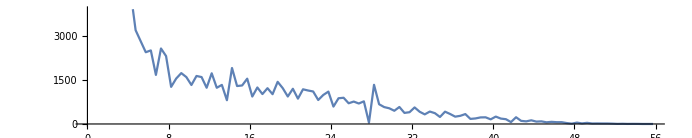

```mathematica
bc=BinCounts[56p0p17[1]⟦All,1⟧,{0,56,0.5}];
ListLinePlot[Transpose[{Range[0.25,56-0.25,0.5],bc}],AspectRatio->0.2]
```

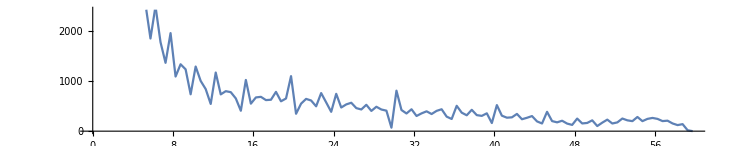

```mathematica
bc=BinCounts[60p0p17[1]⟦All,2⟧,{0,60,0.5}];
ListLinePlot[Transpose[{Range[0.25,60-0.25,0.5],bc}],AspectRatio->0.2]
```

#### Initial & final distributions

These plots are for the initial and final distributions (left, right) for control, LS1, LS2 (red,blue,black), on a z=2arcsin[√p] scale (i.e. on {0,π}. There is an artefactual deficit close to 0, 1.  There is a clear excess of high frequency SNP in LS2 but less clearly in LS1 (right).  Note that these are ‘only’ 200,000 SNP on chromosome 10.

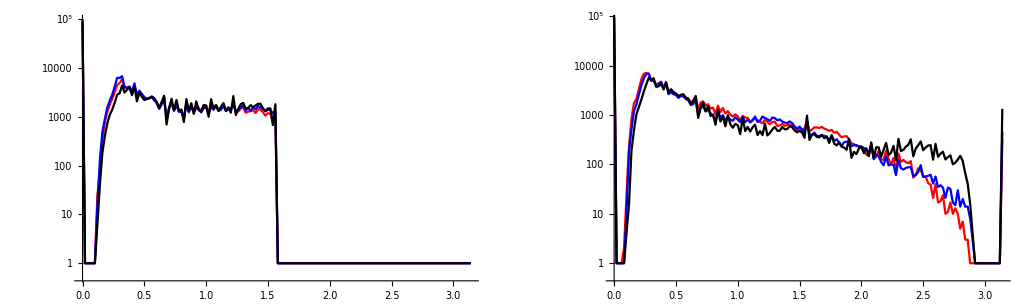

```mathematica
δ=0.02;
bc[j_,k_,δ_]:=BinCounts[arcsin[p0p17C[j]⟦All,k⟧],{0,π+δ,δ}];
gr[k_]:=Show[MapThread[ListLogPlot[Transpose[{Range[0,π,δ],1+bc[#1,k,δ]}],PlotStyle->#2,Joined->True]&,{{0,1,2},{Red,Blue,Black}}]];Show[GraphicsRow[gr/@{1,2}]]
```

There are very many SNP that start at zero but increase. Presumably this is measurement error at low frequency ?  But, the fraction is far higher than Gemma found.

```mathematica
Prepend[Table[Length/@{Select[p0p17C [j],(#⟦1⟧==0)∧(#⟦2⟧==0)&],Select[p0p17C[j],(#⟦1⟧==0)∧(#⟦2⟧>0)&],Select[p0p17C[j],(#⟦1⟧>0)∧(#⟦2⟧==0)&],Select[p0p17C[j],(#⟦1⟧>0)∧(#⟦2⟧>0)&]},{j,0,2}],{"{0,0}","{0,>0}","{>0,0}","{>0,>0}"}]//TableForm
```

{0,0} | {0,>0} | {>0,0} | {>0,>0}
49245 | 45612 | 33170 | 104042
46669 | 39280 | 49035 | 97085
61828 | 36955 | 44751 | 88535

For the control lines, about half the p_0 class have non-zero frequency at the end; the mean frequency is 0.022:

```mathematica
zeroes=Select[p0p17C[0],(#⟦1⟧==0)&];{Count[zeroes,{_,0}],Length[zeroes],Mean[Last/@zeroes]}
```

{49245,94857,0.0224311}

This is the distribution of allele frequencies starting from “zero”:

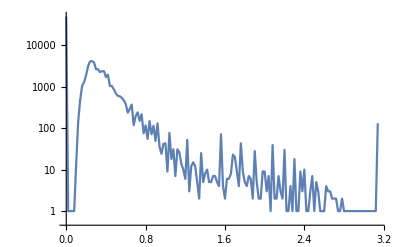

```mathematica
δ=0.02;bcz[δ_]:=BinCounts[arcsin[zeroes⟦All,2⟧],{0,π+δ,δ}];
ListLogPlot[Transpose[{Range[0,π,δ],1+bcz[δ]}],Joined->True]
```

### New frequency data - June 2017

#### getFreqData

```mathematica
getFreqData::usage="getFreqData[c] retrieves data for chromosome c; c=20 is the X chromosome. Defines numSNP[c], posSNP[c], freqSNP[t,r,c], nchrom[t,r]. ";
```

```mathematica
getFreqData::badNum="# of SNP for the different lines and times are inconsistent: `1`";
```

```mathematica
getFreqData[c_Integer]:=Module[{st,stc,nc},
SetDirectory[directoryName[Chrom]];
Do[
st=dataFileName[r]<>"_F"<>ToString[t];
stc=st<>"_"<>chromName[c];
nchrom[t,r]=Get["nchrom_"<>st];
freqSNP[t,r,c]=Get["n_"<>stc];
numSNP[t,r,c]=Length[freqSNP[t,r,c]];
If[t==0&&r==0,posSNP[c]=Get["pos_"<>stc]];,{t,0,17,17},{r,0,2}];
nc=Table[numSNP[t,r,c],{t,0,17,17},{r,0,2}];
If[Length[Union[nc]]≠1,Message[getFreqData::badNum,nc]];
numSNP[c]=numSNP[0,0,c];];
```

#### numSNP

```mathematica
numSNP::usage="numSNP[c] gives the # of SNP on this chromosome. numSNP[t,r,c] lists the # of SNP on each chromosome, as recorded in dataFileName[t,r], which should be the same across all t, r";
```

#### nchrom

```mathematica
nchrom::usage="nchrom[t,r] gives the # of chromosomes in the SNP data; t=0 or 17, r=0, 1, 2";
```

#### freqSNP

```mathematica
freqSNP::usage="freqSNP[t,r,c]  gives the allele counts";
```

#### posSNP

```mathematica
posSNP::usage="posSNP[c] gives the  positions of SNP on the chromosome";
```

#### storeFreqData

```mathematica
storeFreqData::usage="storeFreqData[t,r] retrieves data from each of the 6 .frq files in turn, and  stores it in a series of files, separately for each chromosome. These have the form n_LS1_F0_chr1, storing the numbers of each allele, and pos_LS1_F0_chr1, storing the position of each SNP (which should be the same for all 6 files).  The number of chromosomes is stored in nchrom_LS1_F0_chr1. Prints progress reports.";
```

```mathematica
storeFreqData::badNum="The numbers of chromosomes vary between SNP: `1`";
```

```mathematica
storeFreqData[t:(0|17),r:(0|1|2)]:=Module[{nc,tdc,data,data2,st,c},
st=dataFileName[r]<>"_F"<>ToString[t];
Print["Reading data for t=",t," ",dataFileName[r]];
SetDirectory[directoryName[Data]];
data=Import[dataFileName[t,r],"Data"];
tdc=Tally[data⟦2;;-1,4⟧];
If[Length[tdc]≠1,Message[storeFreqData::badNum,tdc]];
SetDirectory[directoryName[Chrom]];
 nc=Max[First/@tdc];nc>>"nchrom_"<>st;
data2=GatherBy[data⟦2;;-1,{1,2,6}⟧,First];
Print["Storing data for t=",t," ",dataFileName[r]];
Do[Round[nc  data2⟦c,All,3⟧]>>"n_"<>st<>"_"<>chromName[c];
data2⟦c,All,2⟧>>"pos_"<>st<>"_"<>chromName[c];,{c,20}];
Clear[data,data2];];
```

#### dataFileName

```mathematica
dataFileName::usage="dataFileName[t,r] gives the name of the file containing the frequency data for all chromosomes. dataFileName[r] gives the string Ctrl, LS1, LS2. ";
```

```mathematica
dataFileName[0]:="Ctrl";dataFileName[1]:="LS1";dataFileName[2]:="LS2";
dataFileName[t:(0|17),r:(0|1|2)]:="beagle_genMap.all.impute."<>dataFileName[r]<>"_F"<>ToString[t]<>".frq";
```

#### chromName

```mathematica
chromName::usage="chromName[c] gives the name of the chromosome as a string, chr1,… 20 refers to the X chromosome.";
```

```mathematica
chromName[20]="chrX";
chromName[c_Integer]:="chr"<>ToString[c];
```

#### freqPairs

```mathematica
freqPairs::usage="freqPairs[r,c] stores {p_0,p_17} ";
```

```mathematica
freqPairs[r:(0|1|2),c_Integer]:=freqPairs[r,c]=Transpose[{freqSNP[0,r,c]/nchrom[0,r],freqSNP[17,r,c]/nchrom[17,r]}];
```

#### freqDist

```mathematica
freqDist::usage="freqDist[r,c] stores the marginal frequency distribution, expressed as an array";
```

```mathematica
freqDist[r:(0|1|2),c_Integer]:=freqDist[r,c]=Module[{j},
Table[BinCounts[Pick[freqSNP[17,r,c],freqSNP[0,r,c],j],{0,nchrom[17,r]+1,1}],{j,0,nchrom[0,r]}]];
```

#### win

```mathematica
win::usage="win[c,10^4] lists the loci that are contained within successive 10^4 bp windows";
```

```mathematica
win[c_,w_]:=win[c,w]=GatherBy[Range[numSNP[c]],Round[posSNP[c]⟦#⟧/w]&];
```

#### hetM

Beware - there are several het functions around, and terminology changes...

```mathematica
hetM::usage="hetM[t,r,c] gives the mean heterozygosity.  This does not take into account the density of SNP, so it is not the same as π";
```

```mathematica
hetM[t:(0|17),r:(0|1|2),c_Integer]:=Module[{rn,d},
d=If[t==0,Total/@freqDist[r,c],Total[freqDist[r,c]]];
rn=Range[0,1,1/nchrom[t,r]];
((2rn(1.-rn)).d)/Total[d]];
```

#### boundsSNP

```mathematica
boundsSNP::usage="boundsSNP[c] gives the position of the leftmost and the rightmost SNP";
```

```mathematica
boundsSNP[c_]:=boundsSNP[c]=MinMax[posSNP[c]];
```

### New frequency data - August 2017

These allele frequency data have been more heavily filtered, and are supposedly more reliable.

I have just defined parallel definitions, which is not exactly elegant...

#### getFreqDataNew

```mathematica
getFreqDataNew::usage="getFreqDataNew[c] retrieves new data for chromosome c; c=20 is the X chromosome. Defines numSNPNew[c], posSNPNew[c], freqSNPNew[t,r,c], nchromNew[t,r]. ";
```

```mathematica
getFreqDataNew::badNum="# of SNP for the different lines and times are inconsistent: `1`";
```

```mathematica
getFreqDataNew[c_Integer]:=Module[{st,stc,nc},
SetDirectory[directoryNameNew[Chrom,Freqs]];
Do[
st=dataFileName[r]<>"_F"<>ToString[t];
stc=dataFileName[r]<>"_F"<>ToString[t]<>"_"<>chromName[c];
nchromNew[t,r]=Get["nchromNew_"<>st];
freqSNPNew[t,r,c]=Get["nNew_"<>stc];
numSNPNew[t,r,c]=Length[freqSNPNew[t,r,c]];
If[t==0&&r==0,posSNPNew[c]=Get["posNew_"<>stc]];,{t,0,17,17},{r,0,2}];
nc=Table[numSNPNew[t,r,c],{t,0,17,17},{r,0,2}];
If[Length[Union[nc]]≠1,Message[getFreqDataNew::badNum,nc]];
numSNPNew[c]=numSNPNew[0,0,c];];
```

#### storeFreqDataNew

```mathematica
storeFreqDataNew::usage="storeFreqDataNew[r] retrieves data from each of the 3 .frq files in turn, and  stores it in a series of files, separately for each chromosome. These have the form nNew_LS1_F0_chr1, storing the numbers of each allele, and posNew_LS1_F0_chr1, storing the position of each SNP (which should be the same for all 6 files).  The number of chromosomes is stored in nchromNew_LS1_F0_chr1. Prints progress reports.";
```

```mathematica
storeFreqDataNew::badNum="The numbers of chromosomes vary between SNP: `1`";
```

```mathematica
storeFreqDataNew[r:(0|1|2)]:=Module[{nc1,nc2,tdc1,tdc2,data0,data1,data2,st,c},
st[t_]:=dataFileName[r]<>"_F"<>ToString[t];
Print["Reading data from ",dataFileNameNew[r]];
SetDirectory[directoryNameNew[Data,Freqs]];
data0=Import[dataFileNameNew[r],"Data"];
tdc1=Tally[data0⟦2;;-1,4⟧];
tdc2=Tally[data0⟦2;;-1,8⟧];
If[Length[tdc1]≠1∨Length[tdc2]≠1,Message[storeFreqDataNew::badNum,{tdc1,tdc2}]];
Print["Storing data for ",dataFileName[r]];
SetDirectory[directoryNameNew[Chrom,Freqs]];
nc1=Max[First/@tdc1];nc1>>"nchromNew_"<>st[0];
nc2=Max[First/@tdc2];nc2>>"nchromNew_"<>st[17];
data1=GatherBy[data0⟦2;;-1,{1,2,6}⟧,First];
data2=GatherBy[data0⟦2;;-1,{1,2,10}⟧,First];
Do[
Round[nc1  data1⟦c,All,3⟧]>>"nNew_"<>st[0]<>"_"<>chromName[c];
Round[nc2  data2⟦c,All,3⟧]>>"nNew_"<>st[17]<>"_"<>chromName[c];
data1⟦c,All,2⟧>>"posNew_"<>st[0]<>"_"<>chromName[c];,{c,20}];
Clear[data0,data1,data2];];
```

#### dataFileNameNew

```mathematica
dataFileNameNew::usage="dataFileNameNew[t,r] gives the name of the file containing the new frequency data for all chromosomes. The same file holds data for t=0, 17, so dataFileNameNew[r] is also valid. dataFileNameNew[t,r,hets] and dataFileNameNew[r,hets] gives the names of the files that contain the diploid genotypes";
```

```mathematica
dataFileNameNew[t:(0|17),r:(0|1|2)]:=dataFileNameNew[r];
dataFileNameNew[r:(0|1|2)]:="beagle_genMap.all.impute.spectraFiltered.freq."<>dataFileName[r]<>"_F0F17.frq.txt";
dataFileNameNew[t:(0|17),r:(0|1|2),hets]:=dataFileNameNew[r,hets];
dataFileNameNew[r:(0|1|2),hets]:="gathered.output.autoX.GT_full."<>dataFileName[r]<>"_F0F17.aggregate.out.txt";
```

#### directoryNameNew

```mathematica
directoryNameNew::usage="directoryNameNew[Chrom,Freqs] gives the name of the directory containing the new frequency data for each chromosome. directoryNameNew[Data,Freqs] contains the raw allele frequency data. directoryNameNew[Data,Hets] contains the raw diploid genotype data. ";
```

```mathematica
directoryNameNew[Chrom,Freqs]="/Manuscripts/Selection on pedigrees/New data June 2017/Chromosome files new/";
directoryNameNew[Data,Freqs]="/Manuscripts/Selection on pedigrees/New data June 2017/Allele frequencies Aug 7 2017/";
directoryNameNew[Chrom,Hets]="/Manuscripts/Selection on pedigrees/New data June 2017/Diploid genotype chromosome files/";
directoryNameNew[Data,Hets]="/Manuscripts/Selection on pedigrees/New data June 2017/Diploid genotypes Aug 7 2017/";
```

#### directoryName

```mathematica
directoryName::usage="directoryName[Chrom] gives the name of the directory containing the old (June 2017) frequency data for each chromosome. directoryName[Data] contains the raw allele frequency data. directoryName[Ind] gives the directory containing the individual data.";
```

```mathematica
directoryName[Chrom]="/Manuscripts/Selection on pedigrees/New data June 2017/Chromosome files/";
directoryName[Data]="/Manuscripts/Selection on pedigrees/New data June 2017/Longshanks_F0F17.summary_stats/";
directoryName[Ind]="/Manuscripts/Selection on pedigrees/Longshanks/";
```

#### numSNPNew

```mathematica
numSNPNew::usage="numSNPNew[c] gives the # of SNP on this chromosome. numSNPNew[t,r,c] lists the # of SNP on each chromosome, as recorded in dataFileNameNew[r], which should be the same across all t, r";
```

#### nchromNew

```mathematica
nchromNew::usage="nchromNew[t,r] gives the # of chromosomes in the new SNP data; t=0 or 17, r=0, 1, 2";
```

#### freqSNPNew

```mathematica
freqSNPNew::usage="freqSNPNew[t,r,c]  gives the allele counts in the new data";
```

#### posSNPNew

```mathematica
posSNPNew::usage="posSNPNew[c] gives the positions of SNP on the chromosome";
```

#### boundsSNPNew

```mathematica
boundsSNPNew::usage="boundsSNPNew[c] gives the position of the leftmost and the rightmost SNP";
```

```mathematica
boundsSNPNew[c_]:=boundsSNPNew[c]=MinMax[posSNPNew[c]];
```

#### freqPairsNew

```mathematica
freqPairsNew::usage="freqPairsNew[r,c] stores {p_0,p_17} ";
```

```mathematica
freqPairsNew[r:(0|1|2),c_Integer]:=freqPairsNew[r,c]=Transpose[{freqSNPNew[0,r,c]/nchromNew[0,r],freqSNPNew[17,r,c]/nchromNew[17,r]}];
```

#### freqDistNew

```mathematica
freqDistNew::usage="freqDistNew[r,c] stores the marginal frequency distribution, expressed as an array. freqDistNew[r,c,{r_1,…}] uses only loci polymorphic in lines {r_1,…} in the founder generation.";
```

```mathematica
freqDistNew[r:(0|1|2),c_Integer]:=freqDistNew[r,c]=Module[{j},
Table[BinCounts[Pick[freqSNPNew[17,r,c],freqSNPNew[0,r,c],j],{0,nchromNew[17,r]+1,1}],{j,0,nchromNew[0,r]}]];
```

```mathematica
freqDistNew[r:(0|1|2),c_Integer,rl:{(0|1|2)...}]:=freqDistNew[r,c,rl]=
Module[{j,pL=polLoci[0,rl,c]},
Table[BinCounts[Pick[freqSNPNew[17,r,c]⟦pL⟧,freqSNPNew[0,r,c]⟦pL⟧,j],{0,nchromNew[17,r]+1,1}],{j,0,nchromNew[0,r]}]];
```

#### winNew

```mathematica
winNew::usage="winNew[c,10^4] lists the loci that are contained within successive 10^4 bp windows. winNew[c,10^4,r] only counts those that are polymorphic in line r at the start. winNew[c,10^4,{0,17},{1,2}] counts those that are polymorphic in any the given set of populations. Numbering is based on he full set of loci.";
```

```mathematica
winNew[c_,w_]:=winNew[c,w]=GatherBy[Range[numSNPNew[c]],Round[posSNPNew[c]⟦#⟧/w]&];
winNew[c_,w_,r:(0|1|2)]:=winNew[c,w,r]=Module[{i},
Table[Select[winNew[c,w]⟦i⟧,0<freqSNPNew[0,r,c]⟦#⟧<nchromNew[0,r]&],{i,Length[winNew[c,w]]}]];
```

#### winInd

```mathematica
winInd::usage="winInd[c,10^4] lists the loci that are contained within successive 10^4 bp windows, using the individual data. winInd[c,10^4,r] only counts those that are polymorphic in line r at the start. winInd[c,10^4,{0,17},{1,2}] counts those that are polymorphic in any the given set of populations. Numbering is based on the full set of loci.";
```

```mathematica
winInd[c_,w_]:=winInd[c,w]=GatherBy[Range[numSNPInd[c]],Round[posSNPInd[c]⟦#⟧/w]&];
winInd[c_,w_,t:(0|17),r:(0|1|2)]:=winInd[c,w,{t},{r}];
winInd[c_,w_,tl:{(0|17)...},r:(0|1|2)]:=winInd[c,w,tl,{r}];
winInd[c_,w_,tl:{(0|17)...},rl:{(0|1|2)...}]:=winInd[c,w,tl,rl]=
Intersection[polLoci[tl,rl,c],#]&/@winInd[c,w];
```

#### winNewPol

```mathematica
winNewPol::usage="winNewPol[c,10^4,r] lists the loci that are contained within successive 10^4 bp, counting within the set that is polymorphic in line r at the start";
```

```mathematica
winNewPol[c_,w_,r_]:=winNewPol[c,w,r]=Module[{pols,psi},
pols=Pick[Range[numSNPNew[r]],(0<#<nchromNew[0,r])&/@freqSNPNew[0,r,c]];ps=posSNPNew[c]⟦pols⟧;
GatherBy[Range[Length[pols]],Round[ps⟦#⟧/w]&]];
```

#### hetMNew

Beware - there are several het functions around, and terminology changes...

```mathematica
hetMNew::usage="hetMNew[t,r,c] gives the mean heterozygosity.  This does not take into account the density of SNP, so it is not the same as π";
```

```mathematica
hetMNew[t:(0|17),r:(0|1|2),c_Integer]:=Module[{rn,d},
d=If[t==0,Total/@freqDistNew[r,c],Total[freqDistNew[r,c]]];
rn=Range[0,1,1/nchrom[t,r]];
((2rn(1.-rn)).d)/Total[d]];
```

### New utilities August 2017

#### randomSpan

```mathematica
randomSpan::usage="randomSpan[x,n] gives a random interval that is a fraction 0<x<1 of 1;;n";
```

```mathematica
randomSpan[x_,n_Integer]:=Module[{y=RandomReal[{0,1-x}]},
Max[1,Min[n,Round[y*n]]];;Max[1,Min[n,Round[(y+x)n]]]];
```

#### mouseMap, mouseLength

```mathematica
mouseLength::usage="mouseLength[c] gives the length of each chromosome in Mb. mouseLength[] lists all chromosome lengths. Based on the revised Shifman map in Cox et al. 2009.";
```

```mathematica
mouseLength[c_Integer]:=mouseLength[]⟦c⟧;
mouseLength[]:={{3.64,196.26},{3.15,180.99},{5.35,156.5},{3.58,154.42},{3.53,150.23},{3.48,148.41},{3.27,152.14},{4.98,131.42},{6.26,123.10},{4.14,128.39},{3.47,119.17},{5.31,120.30},{4.22,120.13},{8.99,124.00},{3.16,102.99},{3.96,97.13},{3.92,93.60},{3.73,89.74},{3.28,59.96},{5.68,165.35}};
```

```mathematica
mouseMap::usage="mouseMap[c] gives the length of the mouse genetic map in M, based on Cox et al 2009. mouseMap[] gives the full list. The rate for the X is multiplied by 2/3. Based on the revised Shifman map in Cox et al. 2009.";
```

```mathematica
mouseMap[c_Integer]:=mouseMap[]⟦c⟧;
mouseMap[]:={0.9655,1.0182,0.7883,0.8413,0.8697,0.7669,0.8705,0.7396,0.7146,0.7529,0.8085,0.61,0.6485,0.6137,0.564,0.5473,0.5856,0.5667,0.5324,0.7616 2/3};
```

```mathematica
(* MGI map *){1.036,1.07,0.837,0.827,0.85,0.7373,0.719,0.72,0.7,0.68,0.7875,0.6,0.71,0.595,0.598,0.6895,0.526,0.55,0.495,0.725 2/3};
```

This shows the relation between physical and map length. The outlier is the X. The overall ratio is 11.7cM/Mb - much higher than in humans.  The map spans a total of 2.53×10^9 bp

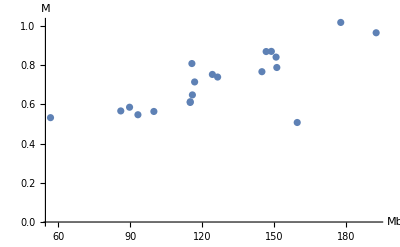

```mathematica
ListPlot[Transpose[{mouseLength[].{-1,1},mouseMap[]}],AxesLabel->{"Mb","M"}]
```

```mathematica
{Total[(100mouseMap[])/(mouseLength[].{-1,1})],Total[mouseLength[].{-1,1}]}
```

{11.7062,2527.13}

#### dzDist

```mathematica
dzDist::usage="dzDist[{r_1,r_2},c,k] stores the joint distribution of Δz between these pairs of lines, allocating to k bins in {-π,π}";
```

```mathematica
dzDist[{r1:(0|1|2),r2:(0|1|2)},c_,k_Integer]:=
dzDist[{r1,r2},c,k]=Module[{zz,dz},
zz[t_,r_]:=arcsin[freqSNPNew[t,r,c]/nchromNew[t,r]];
dz[r_]:=N[zz[17,r]]-N[zz[0,r]];
BinCounts[Transpose[{dz[r1],dz[r2]}//N],{-π,π,(2π)/k},{-π,π,(2π)/k}]];
```

#### simNew

```mathematica
simNew::usage="simNew[r,c,k] makes a simulation based on line r and chromosome c, using DropGenesDiploid. Uses the same initial frequencies (subject to rounding error). Returns the number of copies at each SNP at beginning and end, in the form {{j_0,j_17},…}.  Requires freqSNPNew.";
```

```mathematica
simNew[r:(1|2),c_,k_Integer]:=simNew[r,c,k]=
Module[{j0,pop1,nc=nchromNew[0,r],nped=2Length[pedigree[r]⟦1,1⟧]},
j0=DeleteCases[Round[nped/nc freqSNPNew[0,r,c]],0|nped];
pop1=DropGenesDiploid[makePopDiploidExact[j0,nped/2],Take[pedigree[r],17],Map->mouseMap[c]];
Transpose[{j0,Total[Flatten[pop1⟦-1⟧,1]]}]];
```

#### simFull

```mathematica
simFull::usage="simFull[sim,r,c,k,opts] makes a simulation based on line r and chromosome c, using makeMouseReps. Uses the same initial frequencies (subject to rounding error). This only returns and stores the number of copies at each SNP at beginning and end, in the form {{j_0,j_17},…}, but stores information on blocks as global variables, labelled sim[r,k,θ,numLoci][c]; use clearGlobalVariables[]; resetVariables[]  to save memory. Requires freqSNPNew. ";
```

```mathematica
Options[simFull]={FractionOfVariance->1,NumberOfLoci->All};
```

```mathematica
simFull[sim_,r:(1|2),c_,k_Integer,opts___Rule]:=simFull[sim,r,c,k,opts]=
Module[{j0,pop1,nc=nchromNew[0,r],nped=2Length[pedigree[r]⟦1,1⟧],θ,numLocs},
θ=FractionOfVariance/.{opts}/.Options[makeMouseReps];
numLocs=NumberOfLoci/.{opts}/.Options[makeMouseReps];
j0=DeleteCases[Round[nped/nc freqSNPNew[0,r,c]],0|nped];
makeMouseReps[sim[r,k,θ,numLocs],r,c,j0,0.584,opts];
Transpose[{j0,Total[Flatten[pop[sim[r,k,θ,numLocs][c]]⟦18⟧,1]]}]];
```

#### freqDistSimNew

```mathematica
freqDistSimNew::usage="freqDistSimNew[r,c,k] stores the distribution of {j_0,j_17} for simulated data. freqDistSimNew[r,c,All] stores the mean over 4 replicates";
```

```mathematica
freqDistSimNew[r_,c_,k_]:=freqDistSimNew[r,c,k]=Module[{n0=2Length[pedigree[r]⟦1,1⟧],n17=2Length[pedigree[r]⟦17⟧]},
BinCounts[simNew[r,c,k],{0,n0+1},{0,n17+1}]];
freqDistSimNew[r_,c_,All]:=Mean[Table[freqDistSimNew[r,c,k],{k,4}]];
```

### Simulating conditional on the data

#### makeMouseReps

```mathematica
makeMouseReps::usage="makeMouseReps[sim,r,ρ,𝒦,V_s] makes one simulation for each of the c=1…20 chromosomes, for line r=0, 1, 2.  Simulations are labelled by sim[c]. Each chromosome has ρ discrete loci per Morgan; chromosome lengths are taken from mouseMap[]. By default, selection is spread evenly over the discrete loci, with effects drawn from an exponential. Initial frequencies are determined by makeJList[2n_0,𝒦-1], such that there are 𝒦+1 initial numbers. makeMouseReps[sim,r,c,{j_1,…},V_s] uses specified initial numbers, for chromosome c. Allelic effects are drawn independently for each simulation, and stored in allelicEffects[sim[c]]. FractionOfVariance->ϕ attributes a fraction of the genetic variance θ times the fraction of map; the default is 1. NumberOfLoci->{{x,i_0},…} attributes the genetic variance equally to loci at x, with initial # of copies i_0; this overrides whatever was supplied in {j_1…}.  Here, x is the fractional position along the chromsome, so that x=0.5 would be in the middle. makeMouseReps[sim,r,c,{{{0,…},{1,…}},…},{α_1,…},V_s] uses a specific diploid population and list of allelic effects." ;
```

```mathematica
FractionOfVariance::usage="FractionOfVariance is an option for makeMouseReps that specifies the variance associated with the chromosome, relative to the length of the genetic map; default is 1";
```

```mathematica
NumberOfLoci::usage="NumberOfLoci is an option for makeMouseReps that specifies the loci that affect the trait. Default is All. NumberOfLoci->{{x,j_0},…} specifies the position along the chromosome (between 0 and 1), x, and the initial # of copies, j_0";
```

```mathematica
Options[makeMouseReps]={FractionOfVariance->1,NumberOfLoci->All};
```

```mathematica
makeMouseReps[sim_,r:(0|1|2),c_Integer,j0:{__Integer},Vs_,opts___Rule]:=
Module[{ρ=Length[j0],totalMap=Total[mouseMap[]],n0=Dimensions[pedigree[r]⟦1⟧]⟦2⟧,Ve=1,p0,α,t,fα,nl,θ,ϕ,numLocs,f,jl},
θ=FractionOfVariance/.{opts}/.Options[makeMouseReps];
numLocs=NumberOfLoci/.{opts}/.Options[makeMouseReps];
f[x_List,n_]:=Max[1,Min[n,Round[n*#]]]&/@x;
nl=Length[j0];ϕ=mouseMap[c]/totalMap;
If[numLocs===All,
α=makeAllelicEffects[nl],
jl=List/@f[First/@numLocs,nl];
α=ReplacePart[ConstantArray[0,nl],jl->1];
j0=ReplacePart[j0,Sequence[MapThread[Rule,{jl,Last/@numLocs}]]]];
p0=j0/(2n0)//N;allelicEffects[sim[c]]=fα=α √((2Vs ϕ θ)/(2(α^2).(p0(1-p0))));
makeMouseReps[sim,r,c,makePopDiploidExact[j0,n0],fα,Vs,opts]];
```

```mathematica
makeMouseReps[sim_,r:(0|1|2),c_Integer,pop_List,α_List,Vs_,opts___Rule]:=
Module[{totalMap=Total[mouseMap[]],n0=Dimensions[pedigree[r]⟦1⟧]⟦2⟧,tm=Length[pedigree[r]],Ve=1,nkf,sexL,t,nl,θ,ϕ,numLocs},
θ=FractionOfVariance/.{opts}/.Options[makeMouseReps];
nkf=Table[nKidsByFamily[t,r],{t,tm}];
sexL=sex[#,r]&/@Range[tm];
nl=Length[α];ϕ=mouseMap[c]/totalMap;
allelicEffects[sim[c]]=α;
initialise[sim[c]][n0,pop,2Vs(1-ϕ θ),Ve,zDip[α],mouseMap[c]];
iterateDiploidNew[sim[c],pedigree[r],nkf,sexL,Vs(1-ϕ θ),Ve,zDip[α],mouseMap[c]];];
```

```mathematica
makeMouseReps[sim_,r:(0|1|2),ρ_,𝒦_Integer,Vs_,opts___Rule]:=
Module[{n0=Dimensions[pedigree[r]⟦1⟧]⟦2⟧,j0,nc=Length[mouseMap[]]},
Do[j0=Flatten[ConstantArray[makeJList[2n0,𝒦-1],Round[(ρ mouseMap[c])/𝒦]]];
makeMouseReps[sim,r,c,j0,Vs,opts],{c,nc}]];
```

### Individual data Nov 2017

#### directoryName

```mathematica
directoryName::usage="directoryName[Chrom] gives the name of the directory containing the old (June 2017) frequency data for each chromosome. directoryName[Data] contains the raw allele frequency data. directoryName[Ind] gives the directory containing the individual data.";
```

Defined above

#### dataFileNameHap

```mathematica
dataFileNameHap::usage="dataFileNameHap[t,r,c] gives the name of the file containing the imputed haplotype data for each chromosome. ";
```

```mathematica
dataFileNameHap[t:(0|17),r:(0|1|2),c_Integer]:=
"beagle_genMap.all.impute."<>popNameInd[r]<>genNameInd[t]<>".chr"<>chromNameInd[c]<>".haplo.impute.hap";
```

#### dataFileNameDip

```mathematica
dataFileNameDip::usage="dataFileNameDip[t,r,c] gives the name of the file containing the individual diploid data for each chromosome. ";
```

```mathematica
dataFileNameDip[t:(0|17),r:(0|1|2),c_Integer]:=
"beagle_genMap.all.impute."<>popNameInd[r]<>genNameInd[t]<>".chr"<>chromNameInd[c]<>".diplo.012";
```

#### posFileName

```mathematica
posFileName::usage="posFileName[c] gives the name of the file containing the positions of SNP for each chromosome";
```

```mathematica
posFileName[c_Integer]:=
"beagle_genMap.all.impute.contP0.chr"<>chromNameInd[c]<>".diplo.012.pos";
```

#### indFileName

```mathematica
indFileName::usage="indFileName[t,r] gives the name of the file containing the diploid individuals for each line and time";
```

```mathematica
indFileName[t:(0|17),r:(0|1|2)]:=
"beagle_genMap.all.impute."<>popNameInd[r]<>genNameInd[t]<>".chr1.diplo.012.indv";
```

#### directoryNameInd

```mathematica
directoryNameInd::usage="directoryNameInd[] gives the name of the directory containing the individual data for each chromosome.  ";
```

```mathematica
directoryNameInd[]="/Manuscripts/Selection on pedigrees/Longshanks by chromosome/";
```

#### chromNameInd

```mathematica
chromNameInd::usage="chromNameInd[c] is the name of the chromosome, as a string; 20~X, 21~Y; for individual data";
```

```mathematica
chromNameInd[20]:="X";chromNameInd[21]:="Y";
chromNameInd[c_Integer]:=ToString[c];
```

#### popNameInd

```mathematica
popNameInd::usage="popNameInd[r] is the string giving the control, LS1, LS2 lines";
```

```mathematica
popNameInd[0]="cont";popNameInd[1]="LS1";popNameInd[2]="LS2";
```

#### genNameInd

```mathematica
genNameInd::usage="genNameInd[t] is the string giving P0 or F17";
```

```mathematica
genNameInd[0]="P0";genNameInd[17]="F17";
```

#### numSNPInd

```mathematica
numSNPInd::usage="numSNPInd[c] gives the # of SNP on this chromosome.";
```

#### indsDip

```mathematica
indsDip::usage="indsDip[t,r] gives the individuals in the diploid data";
```

#### freqSNPInd

```mathematica
freqSNPInd::usage="freqSNPInd[t,r,c]  gives the allele counts in the new data, allowing for missing data coded as -1";
```

#### nIndsDip

```mathematica
nIndsDip::usage="nIndsDip[t,r,c]  gives the number of individuals at each site, allowing for missing data coded as -1";
```

#### posSNPInd

```mathematica
posSNPInd::usage="posSNPInd[c] gives the positions of SNP on the chromosome";
```

#### dipInd

```mathematica
dipInd::usage="dipInd[t,r,c] gives the diploid genotype.";
```

#### hapInd

```mathematica
hapInd::usage="hapInd[t,r,c] gives the imputed haploid genotypes, as an array ninds×2×nSNP.";
```

#### getIndData

```mathematica
getIndData::usage="getIndData[c] retrieves individual haploid and diploid data for chromosome c; c=20 is the X chromosome, 21 the Y. Defines numSNPInd[c], posSNPInd[c], freqSNPInd[t,r,c], dipInd[t,r,c], hapInd[t,r,c], inds[t,r]. Progress can be tracked using Dynamic[{t,r}]";
```

```mathematica
getIndData::badNum="# of SNP for time `1`, line `2`, chromosome `3` is inconsistent with posSNPInd";
```

```mathematica
getIndData[c_Integer]:=Module[{},
SetDirectory[directoryName[Ind]];
posSNPInd[c]=Import[posFileName[c],"Data"];
numSNPInd[c]=Length[posSNPInd[c]];
Do[
indsDip[t,r]=Flatten[Import[indFileName[t,r],"Data"]];
dipInd[t,r,c]=Partition[ReadList[dataFileNameDip[t,r,c],Number],
1+Length[posSNPInd[c]]]⟦All,2;;-1⟧;
hapInd[t,r,c]=Partition[Transpose[Partition[
ReadList[dataFileNameHap[t,r,c],Number],2Length[indsDip[t,r]]]],2];
If[Dimensions[dipInd[t,r,c]]≠{Length[indsDip[t,r]],numSNPInd[c]},Message[getIndData::badNum,t,r,c]];
freqSNPInd[t,r,c]=(Mean[DeleteCases[#,-1]]/2)&/@Transpose[dipInd[t,r,c]];
nIndsDip[t,r,c]=Length[DeleteCases[#,-1]]&/@Transpose[dipInd[t,r,c]];,
{t,0,17,17},{r,0,2}]];
```

#### findAncestors

```mathematica
findAncestors::usage="findAncestors[X,{Y_1,…},k] uses excludedDip to count the # of excluded loci, for all pairs of possible parents {Y_i,Y_j}. Returns the sets of parent pairs that have the smallest k values. Returns {{n_1,{{i,j},…}},…}. findAncestors[X,{Y_1,…},k,loci] uses the list of loci provided.";
```

```mathematica
findAncestors[X_List,Y_List,k_Integer]:=findAncestors[X,Y,k,All];
findAncestors[X_List,Y_List,k_Integer,locs_]:=Module[{ninds=Length[Y],tt,i,j,utt},
tt=Table[excludedDip[X,Y⟦{i,j}⟧,locs],{i,1,ninds},{j,1,i}];
utt=Union[Flatten[tt]];
{#,Position[tt,#]}&/@utt⟦1;;Min[k,Length[utt]]⟧];
```

#### findHaploidAncestors

```mathematica
findHaploidAncestors::usage="findHaploidAncestors[X,{{Y_(1, 1),Y_(1, 2)},…},k] finds likely ancestors for all possible haplotypes Y_(i, j). Returns the ancestral haplotypes that have the smallest Hamming distance, in the form {{n_1,{{i,j},…}},…}. findHaploidAncestors[X,{{Y_(1, 1),Y_(1, 2)},…},k,loci] uses the list of loci provided.";
```

```mathematica
findHaploidAncestors[X_List,Y_List,k_Integer]:=findHaploidAncestors[X,Y,k,All];
findHaploidAncestors[X_List,Y_List,k_Integer,locs_]:=Module[{ninds=Length[Y],tt,i,j,utt},
tt=Map[Total[Abs[X⟦locs⟧-#]]&,Y⟦All,All,locs⟧,{2}];
utt=Union[Flatten[tt]];
{#,Position[tt,#]}&/@utt⟦1;;Min[k,Length[utt]]⟧];
```

#### excludedDip

```mathematica
excludedDip::usage="excludedDip[X,{Y,Z}] counts the number of loci in diplotype X that are inconsistent with diplotypes {Y,Z} as ancestors.  excludedDip[X,{Y,Z},loci] uses the list of loci provided.";
```

```mathematica
excludedDip[X_List,{Y_List,Z_List}]:=Count[Transpose[{Y,Z,X}],{0,_,2}|{_,0,2}|{2,_,0}|{_,2,0}|{0,0,1}|{2,2,1}];
excludedDip[X_List,{Y_List,Z_List},locs_]:=excludedDip[X⟦locs⟧,{Y⟦locs⟧,Z⟦locs⟧}];
```

### Analysing individual data February 2018

#### obsTransitionMatrix

```mathematica
obsTransitionMatrix::usage="obsTransitionMatrix[r,c] makes a sparse array that represents the transition matrix between t=0 and 17, for chromosome c, using freqSNPInd.";
```

```mathematica
obsTransitionMatrix[r_,c_]:=
Module[{n0=Length[dipInd[0,t,c]],n17=Length[dipInd[17,t,c]],ft},
ft=Round[Transpose[{2n0 freqSNPInd[0,r,c],2n17 freqSNPInd[17,r,c]}]];
SparseArray[Tally[ft]/.{{k0_,k17_},n_}:>({k0+1,k17+1}->n),{2n0+1,2n17+1}]];
```

#### hyperP

```mathematica
hyperP::usage="hyperP[{j,i},{n_u,n_tot}] gives the probability of sampling j out of n_u, wthout replacement, given that there are i out of n_tot";
```

```mathematica
hyperP[{j_Integer,i_Integer},{nu_Integer,nt_Integer}]:=(Binomial[i,j] Binomial[nt-i,nu-j])/Binomial[nt,nu];
```

#### hyperMLE

How to estimate the distribution in a larger population, size n_t, given a sample of n_s, made without replacement? If we sample k, then k ≤ i ≤k+(n_t-n_s), and the probability of k, given i, is hypergeometric.  The maximum of this wrt i is the MLE. However, choosing this MLE would not make sense: the estimated distribution would only have n_s+1 values, with arbitrary gaps. It seems better to sum the likelihoods, weighting by the probability of k. However,

```mathematica
hyperMLE::usage="hyperMLE[k,{n_s,n_t}] gives the MLE for the # on the whole population, i. hyperMLE[ψ_k,{n_s,n_t}] gives the MLE for ψ_i";
```

```mathematica
hyperMLE[k_Integer,{ns_Integer,nt_Integer}]:=Module[{pp},
pp=hyperP[{k,#},{ns,nt}]&/@Range[k,k+(nt-ns)];
Mean[Flatten[Position[pp,Max[pp]]]]+k-1];
```

```mathematica
hyperMLE[ϕ_List,{ns_Integer,nt_Integer}]:=Module[{i,k},ϕ.Table[hyperP[{k,i},{ns,nt}],{k,0,ns},{i,0,nt}]];
```

Start with an arbitrary initial frequency distribution, ψ:

```mathematica
pp=Range[1/52,51/52,1/52];ff=(pp(1-pp))^(0.2-1);ff=ff/Total[ff];
```

Set up a matrix T_(k,i) giving the hypergeometric sampling distribution. Then, we estimate the parent distribution as ϕ=ψ.T (normalised).  The distribution generated by this would be ψ^*=T.ϕ. Below, the left plot shows ψ, ϕ (red, blue); these are nearly the same. The right plot shows ψ^*/ψ, which differ by about 1% in the bulk, but more at the edges.

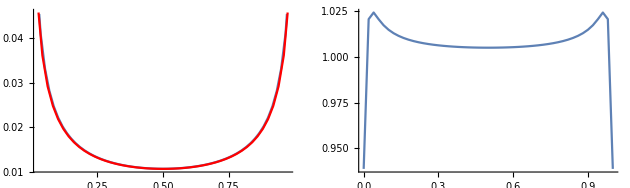

```mathematica
tb=Table[hyperP[{k,i},{50,60}],{k,0,50},{i,0,60}];
ffe=ff.tb;ffe=ffe/Total[ffe];
fff=tb.ffe;
GraphicsRow[{Show[ListLinePlot[Transpose[{Range[0,1,1/60],61/51 ffe}]],ListLinePlot[Transpose[{Range[0,1,1/50],ff}],PlotStyle->Red],PlotRange->All],ListLinePlot[Transpose[{Range[0,1,1/50],fff/ff}],PlotRange->All]}]
```

Note that this is not the same as the distribution of MLE, made SNP by SNP, which would have gaps, with values at only {0,n_s} points.

#### hyperF

```mathematica
hyperF::usage="hyperF[j_0,{k_0,k_17},{n_u,n_0},T] gives the probability of j_0/n_u, given a transition matrix T that gives the probability that j_0+k_0→k_17. hyperF[ψ,{k_0,k_17},{n_u,n_0},T] multiplies by a prior ψ_i";
```

```mathematica
hyperF[j0_Integer,{k0_,k17_},{nu_,nt0_},T_]:=hyperP[{j0,j0+k0},{nu,nt0}]T⟦k0+j0+1,k17+1⟧;
```

```mathematica
hyperF[ψ_,{k0_,k17_},{nu_,nt0_},T_]:=Module[{j},
Sum[ψ⟦k0+j+1⟧ hyperF[j,{k0,k17},{nu,nt0},T],{j,0,nu}]];
```

#### likψ

```mathematica
likψ::usage="likψ[ψ,T,T_obs] gives the likelihood of the distribution ψ_i, assuming a transition matrix T, and with observed # of transitions T_obs";
```

```mathematica
lik[ψ_,T_,Tobs_SparseArray]:=Module[{j,nt0=Length[ψ]-1,nu=Length[Tobs]-1},Total[If[#⟦2⟧==0,0,#⟦2⟧ Log[hyperF[ψ,{#⟦1,1⟧-1,#⟦1,2⟧-1},{nu,nt0},T]]]&/@(ArrayRules[Tobs])]];
```

#### prDip

```mathematica
prDip::usage="prDip[{i_1,i_2},n,p,F] gives the multinomial probability of observing {i_1,i_2}, given p, F";
```

```mathematica
prDip[{i1_Integer,i2_Integer},n_Integer,p_,F_]:=
If[p≤0,If[i1+i2>0,0,1],
If[p≥1,If[n-i1-i2>0,0,1],
Multinomial[n-i1-i2,i1,i2]((1-p)^2+p(1-p)F)^(n-i1-i2)(2p(1-p)(1-F))^i1(p^2+p(1-p)F)^i2]];
```

#### pickLoci

```mathematica
pickLoci::usage="pickLoci[k,t,r,c] picks loci present in k copies";
```

```mathematica
pickLoci[k_,t:(0|17),r:(1|2),c_Integer]:=pickLoci[k,t,r,c]=Module[{n=2Length[dipInd[0,r,c]]},
Pick[Range[numSNPInd[c]],(n#==k)&/@freqSNPInd[t,r,c]]];
```

#### dipConfigs

```mathematica
dipConfigs::usage="dipConfigs[t,r,c] gives the numbers of all configurations of diploid data, in the form {{{i_1,i_2},k},…}. dipConfigs[t,r,c,loci] uses a subset of loci";
```

```mathematica
dipConfigs[t:(0|17),r:(0|1|2),c_Integer]:=dipConfigs[t,r,c,All];
dipConfigs[t:(0|17),r:(0|1|2),c_Integer,loci_]:=Sort[Tally[Drop[BinCounts[#,{0,3}],1]&/@Transpose[dipInd[t,r,c]]⟦loci⟧]];
```

#### estF

```mathematica
estF::usage="estF[t,r,c] estimates the heterozygote deficit, based on diploid data.  estF[t,r,c,loci] uses a subset of loci.";
```

```mathematica
estF[t:(0|17),r:(0|1|2),c_]:=estF[t,r,c,All];estF[t:(0|17),r:(0|1|2),c_,loci_]:=
Module[{n=Length[dipInd[t,r,c]],fd,tfd,dc,logL,j,F},
fd=BinCounts[2n freqSNPInd[t,r,c],{0,2n+1}];tfd=Total[fd];
dc=dipConfigs[t,r,c,loci];
logL=Total[dc/.{{i1_,i2_},k_}:> k Log[1/tfd∑_(j=0)^(2n) fd⟦j+1⟧ prDip[{i1,i2},n,j/(2n),F]]];
F/.FindMaximum[{logL,0≤F≤1},{F,0.75}]⟦2⟧];
```

#### throwP

```mathematica
throwP::usage="throwP[𝒫,haps,t,t^*,r^*,c] assigns haplotypes onto the simulation, at time t, using SNP polymorphic at times t^* and in lines r^*";
```

```mathematica
throwP[𝒫_,h_List,t_,tl_,rl_,c_Integer]:=Module[{cA=configIntervalsAnc[𝒫,t],j},
Flatten[Table[cA⟦j⟧.h⟦All,intSNP[𝒫,t,tl,rl,c]⟦j⟧⟧,{j,Length[cA]}],1]];
```